## Roy equations

## Kinematics

```mathematica
II=IdentityMatrix[3];
Cst={{1/3,1,5/3},{1/3,1/2,-5/6},{1/3,-1/2,1/6}};
Ctu={{1,0,0},{0,-1,0},{0,0,1}};
Csu={{1/3,-1,5/3},{-1/3,1/2,5/6},{1/3,1/2,1/6}};
```

```mathematica
tt[s_,z_]=1/2(sth-s)(1-z);
zp[s_,sp_,z_]=1+(2 tt[s,z])/(sp-sth);
```

### g_2 and g_3

```mathematica
g2[s_,t_,sp_]=-t/(π sp(sp-sth))((sth-s-t) Cst+s Cst.Ctu).(II/(sp-t)+Csu/(sp-sth+t));
g3[s_,t_,sp_]=-(s (sth-s-t))/(π sp(sp-sth+t))(II/(sp-s)+Csu/(sp-sth+s+t));
```

### Partial waves

```mathematica
KT[s_,sp_,z_,Jp_]=(2Jp+1)(g2[s,tt[s,z],sp]+g3[s,tt[s,z],sp]LegendreP[Jp,zp[s,sp,z]]);
```

#### Contributions to I=0

```mathematica
KT00[s_,sp_,z_,Jp_]=FullSimplify[{1,0,0}.KT[s,sp,z,Jp].{1,0,0}];
```

```mathematica
KT01[s_,sp_,z_,Jp_]=FullSimplify[{1,0,0}.KT[s,sp,z,Jp].{0,1,0}];
```

```mathematica
KT02[s_,sp_,z_,Jp_]=FullSimplify[{1,0,0}.KT[s,sp,z,Jp].{0,0,1}];
```

#### Contributions to I=1

```mathematica
KT10[s_,sp_,z_,Jp_]=FullSimplify[{0,1,0}.KT[s,sp,z,Jp].{1,0,0}];
```

```mathematica
KT11[s_,sp_,z_,Jp_]=FullSimplify[{0,1,0}.KT[s,sp,z,Jp].{0,1,0}];
```

```mathematica
KT12[s_,sp_,z_,Jp_]=FullSimplify[{0,1,0}.KT[s,sp,z,Jp].{0,0,1}];
```

#### Contributions to I=2

```mathematica
KT20[s_,sp_,z_,Jp_]=FullSimplify[{0,0,1}.KT[s,sp,z,Jp].{1,0,0}];
```

```mathematica
KT21[s_,sp_,z_,Jp_]=FullSimplify[{0,0,1}.KT[s,sp,z,Jp].{0,1,0}];
```

```mathematica
KT22[s_,sp_,z_,Jp_]=FullSimplify[{0,0,1}.KT[s,sp,z,Jp].{0,0,1}];
```

## Kernels

Log rules

```mathematica
log1 = {Log[sp/(s+sp-sth)]->-Log[1+(s-sth)/sp], -Log[sp]+Log[s+sp-sth]->Log[1+(s-sth)/sp], Log[(s+sp-sth)/sp]->Log[1+(s-sth)/sp], Log[sp]-Log[s+sp-sth]->-Log[1+(s-sth)/sp]};
```

```mathematica
log2 = {Log[2-(2 sp)/(s+2 sp-sth)]->-Log[1-(s-sth)/(2(s+sp-sth))], Log[(s+2 sp-sth)/(2 (s+sp-sth))]->Log[1-(s-sth)/(2(s+sp-sth))]};
```

```mathematica
atanh = {ArcTanh[x_]->1/2Log[(1+x)/(1-x)]};
```

### S0 ()

Contributing:

### I=0

```mathematica
KK00[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT00[s,sp,z,Jp],{z,0,1}]]];
```

S0 to S0

```mathematica
K0000[s_,sp_]=KK00[s,sp,0,0]
```

((-1+(3 s)/(-s+sp)+(2 s+sp)/(-sp+sth))/sp+(2 Log[(s+sp-sth)/sp])/(s-sth))/(3 π)

Cleaned up:

```mathematica
CK0000[s_, sp_]=1/(π (-s+sp))-(2 s+5 sp-4 sth)/(3 π sp(sp-sth))+(2 Log[1+(s-sth)/sp])/(3 π (s-sth));
```

D0 to S0 (worked cleanup example)

```mathematica
K0002[s_, sp_]=KK00[s,sp,0,2]
```

1/(6 π sp (s-sth) (sp-sth)^2)5 ((s-sth) (3 s^2-2 (sp-sth) (2 sp-sth)-5 s (2 sp+sth))-4 sp (sp-sth)^2 Log[sp]+4 sp (sp-sth)^2 Log[s+sp-sth]+24 s sp (s+sp-sth) (Log[2]+Log[s+sp-sth]-Log[s+2 sp-sth]))

```mathematica
Collect[%, Log[x_], FullSimplify]
```

-(5 (-3 s^2+2 (sp-sth) (2 sp-sth)+5 s (2 sp+sth)))/(6 π sp (sp-sth)^2)+(20 s (s+sp-sth) Log[2])/(π (s-sth) (sp-sth)^2)-(10 Log[sp])/(3 π s-3 π sth)+(10 (6 s^2+6 s (sp-sth)+(sp-sth)^2) Log[s+sp-sth])/(3 π (s-sth) (sp-sth)^2)-(20 s (s+sp-sth) Log[s+2 sp-sth])/(π (s-sth) (sp-sth)^2)

```mathematica
(20 s (s+sp-sth) Log[2])/(π (s-sth) (sp-sth)^2)-(10 Log[sp])/(3 π s-3 π sth)+(10 (6 s^2+6 s (sp-sth)+(sp-sth)^2) Log[s+sp-sth])/(3 π (s-sth) (sp-sth)^2)-(20 s (s+sp-sth) Log[s+2 sp-sth])/(π (s-sth) (sp-sth)^2) // FullSimplify
```

```mathematica
FullSimplify[(10 (-(sp-sth)^2 Log[sp]+(6 s^2+6 s (sp-sth)+(sp-sth)^2) Log[s+sp-sth]-6 s (s+sp-sth) Log[1/2 (s+2 sp-sth)]))/(3 π (s-sth) (sp-sth)^2) , sp>s>sth>0]
```

```mathematica
(60 s (s+sp-sth) Log[2-(2 sp)/(s+2 sp-sth)]-10 (sp-sth)^2 Log[sp/(s+sp-sth)])/(3 π (s-sth) (sp-sth)^2)/.log1
```

```mathematica
(10 (sp-sth)^2 Log[.081+(s-sth)/sp]+60 s (s+sp-sth) Log[2-(2 sp)/(s+2 sp-sth)])/(3 π (s-sth) (sp-sth)^2)/.log2
```

(10 (sp-sth)^2 Log[.081+(s-sth)/sp]-60 s (s+sp-sth) Log[1-(s-sth)/(2 (s+sp-sth))])/(3 π (s-sth) (sp-sth)^2)

```mathematica
Apart[-(5 (-3 s^2+2 (sp-sth) (2 sp-sth)+5 s (2 sp+sth)))/(6 π sp (sp-sth)^2) , sth]
```

-5/(3 π sp)+(5 (s^2-5 s sp))/(2 π sp (-sp+sth)^2)-(5 (5 s-2 sp))/(6 π sp (-sp+sth))

Cleaned up :

```mathematica
CK0002[s_, sp_]=-5/(3 π sp)+(5 (s^2-5 s sp))/(2 π sp (-sp+sth)^2)-(5 (5 s-2 sp))/(6 π sp (-sp+sth))+10/(3 π (s-sth))Log[(s-sth)/sp+1]-(20 s (s+sp-sth))/(π (s-sth) (sp-sth)^2)Log[1-(s-sth)/(2 (s+sp-sth))];
```

```mathematica
FullSimplify[CK0002[s, sp]-K0002[s, sp], sp>s>sth>0]
```

0

G0 to S0

```mathematica
K0004[s_, sp_]=KK00[s, sp, 0,4]
```

1/(4 π sp (sp-sth)^4 (-s+sth))(-((s-sth) (21 s^4-12 (sp-sth)^3 (2 sp-sth)-7 s^3 (162 sp+7 sth)+s^2 (-864 sp^2+1266 sp sth+11 sth^2)+s (-228 sp^3+468 sp^2 sth-336 sp sth^2+5 sth^3)))+24 sp ((sp-sth)^4 Log[sp]-(sp-sth)^4 Log[s+sp-sth]+10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (-Log[2 (s+sp-sth)]+Log[s+2 sp-sth])))

```mathematica
CK0004[s_, sp_]=(21 s^4-12 (sp-sth)^3 (2 sp-sth)-7 s^3 (162 sp+7 sth)+s^2 (-864 sp^2+1266 sp sth+11 sth^2)+s (-228 sp^3+468 sp^2 sth-336 sp sth^2+5 sth^3))/(4 π sp (sp-sth)^4)+(6 Log[1+(s-sth)/sp])/(π (s-sth))-(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth))/(π (s-sth) (sp-sth)^4)Log[1-(s-sth)/(2 (s+sp-sth))] ;
```

### I=1

```mathematica
KK01[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT01[s,sp,z,Jp],{z,0,1}]]];
```

P1 to S0

```mathematica
K0011[s_, sp_]=KK01[s, sp, 0,1]
```

(-3 (3 s^2+2 s (sp+2 ⅈ π sp-2 sth)+2 ⅈ π sp (sp-sth)+sth (-2 sp+sth))+6 sp (2 s+sp-sth) (Log[s+sp-sth]-Log[sp (s+2 sp-sth)]+Log[-s-2 sp+sth]))/(π sp (s-sth) (sp-sth))

```mathematica
CK0011[s_, sp_]=-3/(π sp)+(3 (3 s+sp))/(π sp (-sp+sth))+(6 (2 s+sp-sth))/(π (s-sth) (sp-sth))Log[1+(s-sth)/sp];
```

F1 to S0

```mathematica
K0013[s_, sp_]=KK01[s, sp, 0, 3]
```

1/(6 π sp (sp-sth)^3 (-s+sth))7 (10 s^4+15 s^3 (9 sp-sth)+6 s^2 (13 sp^2-41 sp sth+3 sth^2)+6 (sp-sth)^2 (2 ⅈ π sp (sp-sth)+sth (-2 sp+sth))+s (-19 sth^3+3 sp sth^2 (45+8 ⅈ π-40 Log[2])+12 sp^3 (1+2 ⅈ π-10 Log[2])+12 sp^2 sth (-9-4 ⅈ π+20 Log[2]))+24 s sp (sp-sth)^2 Log[sp]+12 sp (-(sp-sth)^2 (12 s+sp-sth) Log[s+sp-sth]-10 s^2 (2 s+3 sp-3 sth) Log[2 (s+sp-sth)]+20 s^3 Log[s+2 sp-sth]+30 s^2 sp Log[s+2 sp-sth]+12 s sp^2 Log[s+2 sp-sth]-30 s^2 sth Log[s+2 sp-sth]-24 s sp sth Log[s+2 sp-sth]+12 s sth^2 Log[s+2 sp-sth]+sp^3 Log[sp (s+2 sp-sth)]-3 sp^2 sth Log[sp (s+2 sp-sth)]+3 sp sth^2 Log[sp (s+2 sp-sth)]-sth^3 Log[sp (s+2 sp-sth)]-(sp-sth)^2 (2 s+sp-sth) Log[-s-2 sp+sth]))

```mathematica
CK0013[s_, sp_]=-7/(π sp)+(35 (s^3+13 s^2 sp-2 s sp^2))/(3 π sp (-sp+sth)^3)-(35 (s^2+17 s sp))/(6 π sp (-sp+sth)^2)+(7 (13 s+6 sp))/(6 π sp (-sp+sth))+(14 (2 s+sp-sth) Log[1+(s-sth)/sp])/(π (s-sth) (sp-sth))+(140 s (s+sp-sth) (2 s+sp-sth) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth) (-sp+sth)^3);
```

### I=2

```mathematica
KK02[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT02[s,sp,z,Jp],{z,0,1}]]];
```

S2 to S0

```mathematica
K0020[s_, sp_]=KK02[s, sp, 0,0]
```

(5 ((s-2 sp+sth)/(sp^2-sp sth)+(2 Log[(s+sp-sth)/sp])/(s-sth)))/(3 π)

```mathematica
CK0020[s_, sp_]=-5/(3 π sp)-(5 (s-sp))/(3 π sp (-sp+sth))+(10 Log[1+(s-sth)/sp])/(3 π (s-sth));
```

D2 to S0

```mathematica
K0022[s_, sp_]=KK02[s, sp, 0,2]
```

1/(6 π sp (sp-sth)^2 (-s+sth))25 (3 s^3+10 s^2 sp+4 s sp^2+4 ⅈ π sp^3-4 (s^2+4 s sp+(1+2 ⅈ π) sp^2) sth+(3 s+6 sp+4 ⅈ π sp) sth^2-2 sth^3-4 sp (sp-sth)^2 Log[s+sp-sth]-24 s sp (s+sp-sth) Log[2 (s+sp-sth)]+4 sp (6 s (s+sp-sth) Log[s+2 sp-sth]+(sp-sth)^2 (Log[sp]+Log[s+2 sp-sth]-Log[-s-2 sp+sth])))

```mathematica
CK0022[s_, sp_]=-25/(3 π sp)-(25 (s^2+3 s sp))/(2 π sp (-sp+sth)^2)+(25 (s+2 sp))/(6 π sp (-sp+sth))+(50 Log[1+(s-sth)/sp])/(3 π s-3 π sth)-(100 s (s+sp-sth) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth) (sp-sth)^2);
```

G2 to S0

```mathematica
K0024[s_, sp_]=KK02[s, sp, 0, 4]
```

1/(16 π sp (sp-sth)^4 (-s+sth))5 (105 s^5+4200 s^4 sp+3600 s^3 sp^2+912 s^2 sp^3+96 s sp^4+96 ⅈ π sp^5-4 (35 s^4+2220 s^3 sp+1404 s^2 sp^2+312 s sp^3+24 (1+4 ⅈ π) sp^4) sth+6 (5 s^3+996 s^2 sp+408 s sp^2+8 (7+12 ⅈ π) sp^3) sth^2-12 (s^2+128 s sp+4 (9+8 ⅈ π) sp^2) sth^3+(65 s+48 (5+2 ⅈ π) sp) sth^4-48 sth^5-96 sp (sp-sth)^4 Log[s+sp-sth]-960 s sp (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[2 (s+sp-sth)]+96 sp (10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[s+2 sp-sth]+(sp-sth)^4 (Log[sp]+Log[s+2 sp-sth]-Log[-s-2 sp+sth])))

```mathematica
CK0024[s_, sp_]=-15/(π sp)-(175 (3 s^4+119 s^3 sp-31 s^2 sp^2+5 s sp^3))/(16 π sp (-sp+sth)^4)+(175 (s^3+134 s^2 sp-15 s sp^2))/(16 π sp (-sp+sth)^3)+(25 (s^2-249 s sp))/(16 π sp (-sp+sth)^2)+(5 (17 s+48 sp))/(16 π sp (-sp+sth))+(30 Log[1+(s-sth)/sp])/(π (s-sth))-(300 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth) (sp-sth)^4);
```

Contributing:

#### I=0

```mathematica
KK10[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT10[s,sp,z,Jp],{z,0,1}]]];
```

S0 to P1

```mathematica
K1100[s_, sp_]=KK10[s, sp, 1,0]
```

-((s-sth) (s^2+12 sp^2-2 (s+6 sp) sth+sth^2)+6 sp (sp-sth) (s+2 sp-sth) (Log[sp]-Log[s+sp-sth]))/(9 π sp (s-sth)^2 (sp-sth))

```mathematica
CK1100[s_, sp_]=-1/(9 π sp)+4/(3 π (-s+sth))+(s-sp)/(9 π sp (-sp+sth))+(2 (s+2 sp-sth) Log[1+(s-sth)/sp])/(3 π (s-sth)^2);
```

D0 to P1

```mathematica
K1102[s_, sp_]=KK10[s, sp, 1,2]
```

1/(18 π sp (s-sth)^2 (sp-sth)^2)5 (3 s^4-7 s^3 (8 sp+sth)+3 s^2 (-24 sp^2+38 sp sth+sth^2)+2 (sp-sth) (sth (12 sp^2-12 sp sth+sth^2)-6 ⅈ π sp (2 sp^2-3 sp sth+sth^2))+3 s (sth^3+8 sp^2 sth (5+ⅈ π-9 Log[2])+sp^3 (-8-4 ⅈ π+48 Log[2])+4 sp sth^2 (-7-ⅈ π+Log[64]))-12 s sp (sp-sth)^2 Log[sp]+12 sp ((sp-sth) (13 s sp+2 sp^2-7 s sth-3 sp sth+sth^2) Log[s+sp-sth]+6 s^2 (s+3 sp-2 sth) Log[2 (s+sp-sth)]-6 s^3 Log[s+2 sp-sth]-18 s^2 sp Log[s+2 sp-sth]-13 s sp^2 Log[s+2 sp-sth]+12 s^2 sth Log[s+2 sp-sth]+20 s sp sth Log[s+2 sp-sth]-7 s sth^2 Log[s+2 sp-sth]-2 sp^3 Log[sp (s+2 sp-sth)]+5 sp^2 sth Log[sp (s+2 sp-sth)]-4 sp sth^2 Log[sp (s+2 sp-sth)]+sth^3 Log[sp (s+2 sp-sth)]+(sp-sth)^2 (s+2 sp-sth) Log[-s-2 sp+sth]))

```mathematica
CK1102[s_, sp_]=-5/(9 π sp)+(20 (s^2+s sp+sp^2))/(3 π (s-sp)^2 (-s+sth))+(5 (s^3-20 s^2 sp-5 s sp^2))/(6 π (s-sp) sp (-sp+sth)^2)-(5 (s^3+69 s sp^2+2 sp^3))/(18 π (s-sp)^2 sp (-sp+sth))+(10 (s+2 sp-sth) Log[1+(s-sth)/sp])/(3 π (s-sth)^2)-(20 s (s+sp-sth) (s+2 sp-sth) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^2 (sp-sth)^2);
```

G0 to P1

```mathematica
K1104[s_, sp_]=KK10[s, sp, 1, 4]
```

1/(16 π sp (s-sth)^2 (sp-sth)^4)(21 s^6-35 s^5 (136 sp+sth)+10 s^4 (-1168 sp^2+1412 sp sth+sth^2)-14 s^3 (584 sp^3-1872 sp^2 sth+1092 sp sth^2+sth^3)+s^2 (-1920 sp^4+13488 sp^3 sth-19344 sp^2 sth^2+7304 sp sth^3+17 sth^4)+16 (sp-sth)^3 (sth (12 sp^2-12 sp sth+sth^2)-6 ⅈ π sp (2 sp^2-3 sp sth+sth^2))+s (17 sth^5+128 sp^2 sth^3 (44+3 ⅈ π-75 Log[2])+384 sp^4 sth (7+ⅈ π-35 Log[2])+96 sp^5 (-2-ⅈ π+40 Log[2])+144 sp^3 sth^2 (-45-4 ⅈ π+120 Log[2])+16 sp sth^4 (-101-6 ⅈ π+120 Log[2]))-96 s sp (sp-sth)^4 Log[sp]+96 sp ((sp-sth)^3 (sp (41 s+2 sp)-3 (7 s+sp) sth+sth^2) Log[s+sp-sth]+10 s^2 (7 s^3+7 s^2 (4 sp-3 sth)+s (37 sp-23 sth) (sp-sth)+(20 sp-11 sth) (sp-sth)^2) Log[2 (s+sp-sth)]-70 s^5 Log[s+2 sp-sth]-280 s^4 sp Log[s+2 sp-sth]-370 s^3 sp^2 Log[s+2 sp-sth]-200 s^2 sp^3 Log[s+2 sp-sth]-41 s sp^4 Log[s+2 sp-sth]+210 s^4 sth Log[s+2 sp-sth]+600 s^3 sp sth Log[s+2 sp-sth]+510 s^2 sp^2 sth Log[s+2 sp-sth]+144 s sp^3 sth Log[s+2 sp-sth]-230 s^3 sth^2 Log[s+2 sp-sth]-420 s^2 sp sth^2 Log[s+2 sp-sth]-186 s sp^2 sth^2 Log[s+2 sp-sth]+110 s^2 sth^3 Log[s+2 sp-sth]+104 s sp sth^3 Log[s+2 sp-sth]-21 s sth^4 Log[s+2 sp-sth]-2 sp^5 Log[sp (s+2 sp-sth)]+9 sp^4 sth Log[sp (s+2 sp-sth)]-16 sp^3 sth^2 Log[sp (s+2 sp-sth)]+14 sp^2 sth^3 Log[sp (s+2 sp-sth)]-6 sp sth^4 Log[sp (s+2 sp-sth)]+sth^5 Log[sp (s+2 sp-sth)]+(sp-sth)^4 (s+2 sp-sth) Log[-s-2 sp+sth]))

```mathematica
CK1104[s_, sp_]=-1/(π sp)+(12 (s^4+6 s^3 sp+21 s^2 sp^2+6 s sp^3+sp^4))/(π (s-sp)^4 (-s+sth))+(7 (3 s^5-682 s^4 sp-332 s^3 sp^2+58 s^2 sp^3-7 s sp^4))/(16 π (s-sp) sp (-sp+sth)^4)+(7 (s^5+656 s^4 sp-1294 s^3 sp^2-344 s^2 sp^3+21 s sp^4))/(16 π (s-sp)^2 sp (-sp+sth)^3)+(3 s^5-1382 s^4 sp+2208 s^3 sp^2-7002 s^2 sp^3-547 s sp^4)/(16 π (s-sp)^3 sp (-sp+sth)^2)+(-15 s^5+44 s^4 sp-1946 s^3 sp^2-2916 s^2 sp^3-1871 s sp^4-16 sp^5)/(16 π (s-sp)^4 sp (-sp+sth))+(6 (s+2 sp-sth) Log[1+(s-sth)/sp])/(π (s-sth)^2)-(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s+2 sp-sth) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^2 (sp-sth)^4);
```

### I=1

```mathematica
KK11[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT11[s,sp,z,Jp],{z,0,1}]]];
```

P1 to P1

```mathematica
K1111[s_, sp_]=KK11[s, sp, 1, 1]
```

1/(2 π sp (-s+sp) (s-sth)^2 (sp-sth))(3 s^4+s^3 ((23+12 ⅈ π) sp-9 sth)+3 s^2 ((-4+6 ⅈ π) sp^2+(-11-6 ⅈ π) sp sth+3 sth^2)+3 s ((-4-6 ⅈ π) sp^3+8 sp^2 sth+(3+2 ⅈ π) sp sth^2-sth^3)+sp (sth (12 sp^2-12 sp sth+sth^2)-6 ⅈ π sp (2 sp^2-3 sp sth+sth^2))-6 (s-sp) sp (2 s+sp-sth) (s+2 sp-sth) (Log[s+sp-sth]-Log[sp (s+2 sp-sth)]+Log[-s-2 sp+sth]))

```mathematica
CK1111[s_, sp_]=1/(π (-s+sp))-6/(π (s-sth))+(3 (s-sth))/(2 π sp sth)+(-3 s^2-20 s sth-sth^2)/(2 π (s-sth) (sp-sth) sth)-(3 (2 s+sp-sth) (s+2 sp-sth) Log[1+(s-sth)/sp])/(π (s-sth)^2 (-sp+sth));
```

F1 to P1

```mathematica
K1113[s_, sp_]=KK11[s, sp, 1, 3]
```

1/(12 π sp (s-sth)^2 (sp-sth)^3)(-7 (s-sth) (s^4+s^3 (171 sp-4 sth)+2 (sp-sth)^2 (12 sp^2-12 sp sth+sth^2)+s^2 (332 sp^2-256 sp sth+7 sth^2)+s (168 sp^3-310 sp^2 sth+137 sp sth^2-6 sth^3))+840 s sp (sp-sth) (7 s sp+2 sp^2-4 s sth-3 sp sth+sth^2) Log[2]+84 sp (-(sp-sth)^2 (2 s+sp-sth) (s+2 sp-sth) Log[sp]+(6 s^2 (12 sp-7 sth)+s (25 sp-13 sth) (sp-sth)+(sp-sth)^2 (2 sp-sth)) (sp-sth) Log[s+sp-sth]+10 s^3 (2 s+7 sp-5 sth) Log[2 (s+sp-sth)]-10 s (s+sp-sth) (2 s+sp-sth) (s+2 sp-sth) Log[s+2 sp-sth]))

```mathematica
CK1113[s_, sp_]=-7/(6 π sp)-(14 (s^3+4 s^2 sp+4 s sp^2+sp^3))/(π (s-sp)^3 (-s+sth))+(7 (s^4+167 s^3 sp+83 s^2 sp^2-11 s sp^3))/(12 π (s-sp) sp (-sp+sth)^3)-(7 (3 s^4+71 s^3 sp-271 s^2 sp^2-43 s sp^3))/(12 π (s-sp)^2 sp (-sp+sth)^2)+(7 (2 s^4+17 s^3 sp+21 s^2 sp^2+79 s sp^3+sp^4))/(6 π (s-sp)^3 sp (-sp+sth))+(7 (2 s+sp-sth) (s+2 sp-sth) Log[1+(s-sth)/sp])/(π (s-sth)^2 (sp-sth))+(70 s (s+sp-sth) (2 s+sp-sth) (s+2 sp-sth) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^2 (-sp+sth)^3);
```

### I=2

```mathematica
KK12[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT12[s,sp,z,Jp],{z,0,1}]]];
```

S2 to P1

```mathematica
K1120[s_, sp_]=KK12[s, sp, 1, 0]
```

(5 ((s-sth) (s^2+12 sp^2-2 (s+6 sp) sth+sth^2)+6 sp (sp-sth) (s+2 sp-sth) (Log[sp]-Log[s+sp-sth])))/(18 π sp (s-sth)^2 (sp-sth))

```mathematica
CK1120[s_, sp_]=5/(18 π sp)-10/(3 π (-s+sth))+(5 (-s+sp))/(18 π sp (-sp+sth))-(5 (s+2 sp-sth) Log[1+(s-sth)/sp])/(3 π (s-sth)^2);
```

D2 to P1

```mathematica
K1122[s_, sp_]=KK12[s, sp, 1,2]
```

1/(36 π sp (s-sth)^2 (sp-sth)^2)25 (-((s-sth) (3 s^3-4 s^2 (14 sp+sth)-s (72 sp^2-58 sp sth+sth^2)-2 (sp-sth) (12 sp^2-12 sp sth+sth^2)))-72 s sp (-2 sp+sth) (-sp+sth) Log[2]+12 sp ((sp-sth)^2 (s+2 sp-sth) Log[sp]-(sp-sth) (13 s sp+2 sp^2-7 s sth-3 sp sth+sth^2) Log[s+sp-sth]+6 s (-s (s+3 sp-2 sth) Log[2 (s+sp-sth)]+(s+sp-sth) (s+2 sp-sth) Log[s+2 sp-sth])))

```mathematica
CK1122[s_, sp_]=25/(18 π sp)-(50 (s^2+s sp+sp^2))/(3 π (s-sp)^2 (-s+sth))-(25 (s^3-20 s^2 sp-5 s sp^2))/(12 π (s-sp) sp (-sp+sth)^2)+(25 (s^3+69 s sp^2+2 sp^3))/(36 π (s-sp)^2 sp (-sp+sth))-(25 (s+2 sp-sth) Log[1+(s-sth)/sp])/(3 π (s-sth)^2)+(50 s (s+sp-sth) (s+2 sp-sth) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^2 (sp-sth)^2);
```

G2 to P1

```mathematica
K1124[s_, sp_]=KK12[s, sp, 1, 4]
```

1/(32 π sp (s-sth)^2 (sp-sth)^4)5 (-21 s^6+35 s^5 (136 sp+sth)+10 s^4 (1168 sp^2-1412 sp sth-sth^2)+14 s^3 (584 sp^3-1872 sp^2 sth+1092 sp sth^2+sth^3)+s^2 (1920 sp^4-13488 sp^3 sth+19344 sp^2 sth^2-7304 sp sth^3-17 sth^4)+16 (sp-sth)^3 (-sth (12 sp^2-12 sp sth+sth^2)+6 ⅈ π sp (2 sp^2-3 sp sth+sth^2))+s (-17 sth^5+144 sp^3 sth^2 (45+4 ⅈ π-120 Log[2])+16 sp sth^4 (101+6 ⅈ π-120 Log[2])+96 sp^5 (2+ⅈ π-40 Log[2])+384 sp^4 sth (-7-ⅈ π+35 Log[2])+128 sp^2 sth^3 (-44-3 ⅈ π+75 Log[2]))+96 s sp (sp-sth)^4 Log[sp]+96 sp (-(sp-sth)^3 (sp (41 s+2 sp)-3 (7 s+sp) sth+sth^2) Log[s+sp-sth]-10 s^2 (7 s^3+7 s^2 (4 sp-3 sth)+s (37 sp-23 sth) (sp-sth)+(20 sp-11 sth) (sp-sth)^2) Log[2 (s+sp-sth)]+70 s^5 Log[s+2 sp-sth]+280 s^4 sp Log[s+2 sp-sth]+370 s^3 sp^2 Log[s+2 sp-sth]+200 s^2 sp^3 Log[s+2 sp-sth]+41 s sp^4 Log[s+2 sp-sth]-210 s^4 sth Log[s+2 sp-sth]-600 s^3 sp sth Log[s+2 sp-sth]-510 s^2 sp^2 sth Log[s+2 sp-sth]-144 s sp^3 sth Log[s+2 sp-sth]+230 s^3 sth^2 Log[s+2 sp-sth]+420 s^2 sp sth^2 Log[s+2 sp-sth]+186 s sp^2 sth^2 Log[s+2 sp-sth]-110 s^2 sth^3 Log[s+2 sp-sth]-104 s sp sth^3 Log[s+2 sp-sth]+21 s sth^4 Log[s+2 sp-sth]+2 sp^5 Log[sp (s+2 sp-sth)]-9 sp^4 sth Log[sp (s+2 sp-sth)]+16 sp^3 sth^2 Log[sp (s+2 sp-sth)]-14 sp^2 sth^3 Log[sp (s+2 sp-sth)]+6 sp sth^4 Log[sp (s+2 sp-sth)]-sth^5 Log[sp (s+2 sp-sth)]-(sp-sth)^4 (s+2 sp-sth) Log[-s-2 sp+sth]))

```mathematica
CK1124[s_, sp_]=5/(2 π sp)-(30 (s^4+6 s^3 sp+21 s^2 sp^2+6 s sp^3+sp^4))/(π (s-sp)^4 (-s+sth))-(35 (3 s^5-682 s^4 sp-332 s^3 sp^2+58 s^2 sp^3-7 s sp^4))/(32 π (s-sp) sp (-sp+sth)^4)-(35 (s^5+656 s^4 sp-1294 s^3 sp^2-344 s^2 sp^3+21 s sp^4))/(32 π (s-sp)^2 sp (-sp+sth)^3)-(5 (3 s^5-1382 s^4 sp+2208 s^3 sp^2-7002 s^2 sp^3-547 s sp^4))/(32 π (s-sp)^3 sp (-sp+sth)^2)+(5 (15 s^5-44 s^4 sp+1946 s^3 sp^2+2916 s^2 sp^3+1871 s sp^4+16 sp^5))/(32 π (s-sp)^4 sp (-sp+sth))-(15 (s+2 sp-sth) Log[1+(s-sth)/sp])/(π (s-sth)^2)+(150 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s+2 sp-sth) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^2 (sp-sth)^4);
```

### I=0

```mathematica
KK20[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT20[s,sp,z,Jp],{z,0,1}]]];
```

S0 to S2

```mathematica
K2000[s_, sp_]=KK20[s, sp, 0,0]
```

((s-2 sp+sth)/(sp^2-sp sth)+(2 Log[(s+sp-sth)/sp])/(s-sth))/(3 π)

```mathematica
CK2000[s_, sp_]=-1/(3 π sp)+(-s+sp)/(3 π sp (-sp+sth))+(2 Log[1+(s-sth)/sp])/(3 π (s-sth));
```

D0 to S2

```mathematica
K2002[s_, sp_]=KK20[s, sp, 0, 2]
```

1/(6 π sp (sp-sth)^2 (-s+sth))5 (3 s^3+10 s^2 sp+4 s sp^2+4 ⅈ π sp^3-4 (s^2+4 s sp+(1+2 ⅈ π) sp^2) sth+(3 s+6 sp+4 ⅈ π sp) sth^2-2 sth^3-4 sp (sp-sth)^2 Log[s+sp-sth]-24 s sp (s+sp-sth) Log[2 (s+sp-sth)]+4 sp (6 s (s+sp-sth) Log[s+2 sp-sth]+(sp-sth)^2 (Log[sp]+Log[s+2 sp-sth]-Log[-s-2 sp+sth])))

```mathematica
CK2002[s_, sp_]=-5/(3 π sp)-(5 (s^2+3 s sp))/(2 π sp (-sp+sth)^2)+(5 (s+2 sp))/(6 π sp (-sp+sth))+(10 Log[1+(s-sth)/sp])/(3 π s-3 π sth)+(20 s (s+sp-sth) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (sp-sth)^2 (-s+sth));
```

G0 to S2

```mathematica
K2004[s_, sp_]=KK20[s, sp, 0,4]
```

1/(16 π sp (sp-sth)^4 (-s+sth))(105 s^5+4200 s^4 sp+3600 s^3 sp^2+912 s^2 sp^3+96 s sp^4+96 ⅈ π sp^5-4 (35 s^4+2220 s^3 sp+1404 s^2 sp^2+312 s sp^3+24 (1+4 ⅈ π) sp^4) sth+6 (5 s^3+996 s^2 sp+408 s sp^2+8 (7+12 ⅈ π) sp^3) sth^2-12 (s^2+128 s sp+4 (9+8 ⅈ π) sp^2) sth^3+(65 s+48 (5+2 ⅈ π) sp) sth^4-48 sth^5-96 sp (sp-sth)^4 Log[s+sp-sth]-960 s sp (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[2 (s+sp-sth)]+96 sp (10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[s+2 sp-sth]+(sp-sth)^4 (Log[sp]+Log[s+2 sp-sth]-Log[-s-2 sp+sth])))

```mathematica
CK2004[s_, sp_]=-3/(π sp)-(35 (3 s^4+119 s^3 sp-31 s^2 sp^2+5 s sp^3))/(16 π sp (-sp+sth)^4)+(35 (s^3+134 s^2 sp-15 s sp^2))/(16 π sp (-sp+sth)^3)+(5 (s^2-249 s sp))/(16 π sp (-sp+sth)^2)+(17 s+48 sp)/(16 π sp (-sp+sth))+(6 Log[1+(s-sth)/sp])/(π s-π sth)-(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth) (sp-sth)^4);
```

### I=1

```mathematica
KK21[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT21[s,sp,z,Jp],{z,0,1}]]];
```

P1 to S2

```mathematica
K2011[s_, sp_]=KK21[s, sp, 0,1]
```

(9 s^2+6 s (sp+2 ⅈ π sp-2 sth)+6 ⅈ π sp (sp-sth)+3 sth (-2 sp+sth)-6 sp (2 s+sp-sth) (Log[s+sp-sth]-Log[sp (s+2 sp-sth)]+Log[-s-2 sp+sth]))/(2 π sp (s-sth) (sp-sth))

```mathematica
CK2011[s_, sp_]=3/(2 π sp)-(3 (3 s+sp))/(2 π sp (-sp+sth))-(3 (2 s+sp-sth) Log[1+(s-sth)/sp])/(π (s-sth) (sp-sth));
```

F1 to S2

```mathematica
K2013[s_, sp_]=KK21[s, sp, 0,3]
```

1/(12 π sp (sp-sth)^3 (-s+sth))7 (-10 s^4+15 s^3 (-9 sp+sth)+6 (sp-sth)^2 (-2 ⅈ π sp (sp-sth)+(2 sp-sth) sth)-6 s^2 (13 sp^2-41 sp sth+3 sth^2)+s (19 sth^3+12 sp^2 sth (9+4 ⅈ π-20 Log[2])+3 sp sth^2 (-45-8 ⅈ π+40 Log[2])+12 sp^3 (-1-2 ⅈ π+Log[1024]))-24 s sp (sp-sth)^2 Log[sp]+12 sp ((sp-sth)^2 (12 s+sp-sth) Log[s+sp-sth]+10 s^2 (2 s+3 sp-3 sth) Log[2 (s+sp-sth)]-20 s^3 Log[s+2 sp-sth]-30 s^2 sp Log[s+2 sp-sth]-12 s sp^2 Log[s+2 sp-sth]+30 s^2 sth Log[s+2 sp-sth]+24 s sp sth Log[s+2 sp-sth]-12 s sth^2 Log[s+2 sp-sth]-sp^3 Log[sp (s+2 sp-sth)]+3 sp^2 sth Log[sp (s+2 sp-sth)]-3 sp sth^2 Log[sp (s+2 sp-sth)]+sth^3 Log[sp (s+2 sp-sth)]+(sp-sth)^2 (2 s+sp-sth) Log[-s-2 sp+sth]))

```mathematica
CK2013[s_, sp_]=7/(2 π sp)-(35 (s^3+13 s^2 sp-2 s sp^2))/(6 π sp (-sp+sth)^3)+(35 (s^2+17 s sp))/(12 π sp (-sp+sth)^2)-(7 (13 s+6 sp))/(12 π sp (-sp+sth))+(7 (2 s+sp-sth) Log[1+(s-sth)/sp])/(π (s-sth) (-sp+sth))-(70 s (s+sp-sth) (2 s+sp-sth) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth) (-sp+sth)^3);
```

### I=2

```mathematica
KK22[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT22[s,sp,z,Jp],{z,0,1}]]];
```

S2 to S2

```mathematica
K2020[s_, sp_]=KK22[s, sp, 0,0]
```

((-1+(6 s)/(-s+sp)+(5 s+sp)/(-sp+sth))/sp+(2 Log[(s+sp-sth)/sp])/(s-sth))/(6 π)

```mathematica
CK2020[s_, sp_]=1/(π (-s+sp))+(5 s-7 sth)/(6 π sp sth)+(-5 s-sth)/(6 π (sp-sth) sth)+Log[1+(s-sth)/sp]/(3 π s-3 π sth);
```

D2 to S2

```mathematica
K2022[s_, sp_]=KK22[s, sp, 0,2]
```

1/(12 π sp (s-sth) (sp-sth)^2)5 ((s-sth) (9 s^2-10 s sp-4 sp^2-11 s sth+6 sp sth-2 sth^2)-4 sp (sp-sth)^2 Log[sp]+4 sp (sp-sth)^2 Log[s+sp-sth]+24 s sp (s+sp-sth) (Log[2]+Log[s+sp-sth]-Log[s+2 sp-sth]))

```mathematica
CK2022[s_, sp_]=-5/(6 π sp)+(5 (3 s^2-7 s sp))/(4 π sp (-sp+sth)^2)-(5 (11 s-2 sp))/(12 π sp (-sp+sth))+(5 Log[1+(s-sth)/sp])/(3 π s-3 π sth)-(10 s (s+sp-sth) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth) (sp-sth)^2);
```

G2 to S2

```mathematica
K2024[s_, sp_]=KK22[s, sp, 0,4]
```

1/(32 π sp (sp-sth)^4 (-s+sth))(-((s-sth) (273 s^4-48 (sp-sth)^3 (2 sp-sth)-7 s^3 (696 sp+61 sth)+s^2 (-3312 sp^2+5448 sp sth+83 sth^2)+s (-912 sp^3+1728 sp^2 sth-1392 sp sth^2+23 sth^3)))+96 sp ((sp-sth)^4 Log[sp]-(sp-sth)^4 Log[s+sp-sth]+10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (-Log[2 (s+sp-sth)]+Log[s+2 sp-sth])))

```mathematica
CK2024[s_, sp_]=-3/(2 π sp)-(7 (-39 s^4+757 s^3 sp-317 s^2 sp^2+79 s sp^3))/(32 π sp (-sp+sth)^4)-(7 (61 s^3-802 s^2 sp+141 s sp^2))/(32 π sp (-sp+sth)^3)+(83 s^2-1323 s sp)/(32 π sp (-sp+sth)^2)+(23 s+48 sp)/(32 π sp (-sp+sth))+(3 Log[1+(s-sth)/sp])/(π s-π sth)-(30 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth) (sp-sth)^4);
```

### I=0

```mathematica
KK00[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT00[s,sp,z,Jp],{z,0,1}]]];
```

S0 to D0

```mathematica
K0200[s_ ,sp_]=KK00[s, sp, 2,0]
```

(2 (-3 (s-sth) (s+2 sp-sth)-(s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) (Log[sp]-Log[s+sp-sth])))/(3 π (s-sth)^3)

```mathematica
CK0200[s_, sp_]=-(4 sp)/(π (-s+sth)^2)+2/(π (-s+sth))+(2 (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1+(s-sth)/sp])/(3 π (s-sth)^3);
```

D0 to D0

```mathematica
K0202[s_, sp_]=KK00[s, sp, 2, 2]
```

-1/(24 π (s-sp) sp (s-sth)^3 (sp-sth)^2)(3 (s-sth) (3 s^5+s^4 (125 sp-17 sth)-80 sp^2 (sp-sth)^2 (2 sp-sth)+3 s^3 (160 sp^2-85 sp sth+11 sth^2)-s^2 (40 sp^3+520 sp^2 sth-215 sp sth^2+27 sth^3)+s (-400 sp^4+360 sp^3 sth+120 sp^2 sth^2-85 sp sth^3+8 sth^4))-80 (s-sp) sp (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) (-(sp-sth)^2 Log[sp]+(6 s^2+6 s sp+(sp-sth)^2) Log[s+sp-sth]+s ((s+sp) Log[64]-6 sth Log[2 (s+sp-sth)]-6 (s+sp-sth) Log[s+2 sp-sth])))

```mathematica
CK0202[s_, sp_]=-1/(π (s-sp))-(3 s^2)/(8 π sp (sp-sth)^2)-(s (128 sp-11 sth))/(8 π sp (sp-sth)^2)-(76 sp^2-2 sp sth+sth^2)/(π sp (sp-sth)^2)-(5 (14 sp^2+11 sp sth+2 sth^2))/(π (s-sth) (sp-sth)^2)-(20 (sp^3+sp^2 sth+sp sth^2))/(π (s-sth)^2 (sp-sth)^2)+(10 (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1+(s-sth)/sp])/(3 π (s-sth)^3)-(20 s (s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^3 (sp-sth)^2);
```

G0 to D0

```mathematica
K0204[s_, sp_]=KK00[s, sp, 2, 4]
```

1/(8 π sp (sp-sth)^4 (-s+sth)^3)(15 s^7+s^6 (2367 sp-91 sth)-144 sp (sp-sth)^4 (2 sp-sth) sth+10 s^5 (1509 sp^2-936 sp sth+20 sth^2)+10 s^4 (2340 sp^3-4668 sp^2 sth+1449 sp sth^2-19 sth^3)+5 s^3 (2736 sp^4-10944 sp^3 sth+10620 sp^2 sth^2-2196 sp sth^3+11 sth^4)+2 s (144 sp^6-2160 sp^5 sth+6120 sp^4 sth^2-6840 sp^3 sth^3+3225 sp^2 sth^4-450 sp sth^5-7 sth^6-480 sp (sp-sth)^3 (6 sp^2-6 sp sth+sth^2) Log[2])+s^2 (3024 sp^5-23616 sp^4 sth+42984 sp^3 sth^2-27096 sp^2 sth^3+4239 sp sth^4+25 sth^5-480 sp (sp-sth)^2 (66 sp^2-70 sp sth+13 sth^2) Log[2])+48 sp ((sp-sth)^4 (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[sp]-(sp-sth)^2 ((sp-sth)^2 (6 sp^2-6 sp sth+sth^2)+2 s (sp-sth) (63 sp^2-64 sp sth+11 sth^2)+s^2 (661 sp^2-702 sp sth+131 sth^2)) Log[s+sp-sth]-10 s^3 (7 s^3+28 s^2 (2 sp-sth)+2 (sp-sth) (70 sp^2-80 sp sth+17 sth^2)+s (135 sp^2-172 sp sth+44 sth^2)) Log[2 (s+sp-sth)]+10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[s+2 sp-sth]))

```mathematica
CK0204[s_, sp_]=-(15 s^4)/(8 π sp (sp-sth)^4)-(s^3 (2367 sp-46 sth))/(8 π sp (sp-sth)^4)-(45 sp (38 sp^2+43 sp sth+10 sth^2))/(π (sp-sth)^4)-(s^2 (15090 sp^2-2259 sp sth+17 sth^2))/(8 π sp (sp-sth)^4)-(s (11700 sp^3-705 sp^2 sth+306 sp sth^2+7 sth^3))/(4 π sp (sp-sth)^4)-(9 (42 sp^4+242 sp^3 sth+267 sp^2 sth^2+42 sp sth^3+2 sth^4))/(π (s-sth) (sp-sth)^4)-(36 (sp^5+6 sp^4 sth+21 sp^3 sth^2+6 sp^2 sth^3+sp sth^4))/(π (s-sth)^2 (sp-sth)^4)+(6 (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1+(s-sth)/sp])/(π (s-sth)^3)-(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^3 (sp-sth)^4);
```

### I=1

```mathematica
KK01[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT01[s,sp,z,Jp],{z,0,1}]]];
```

P1 to D0

```mathematica
K0211[s_, sp_]=KK01[s, sp, 2, 1]
```

1/(π (s-sth)^3 (sp-sth))6 (2 s+sp-sth) (-ⅈ ((-3 ⅈ+π) s^2+6 (-ⅈ+π) s sp+6 π sp^2-2 (-3 ⅈ+π) s sth-6 (-ⅈ+π) sp sth+(-3 ⅈ+π) sth^2)+(s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) (Log[s+sp-sth]-Log[sp (s+2 sp-sth)]+Log[-s-2 sp+sth]))

```mathematica
CK0211[s_, sp_]=-(36 sp)/(π (s-sth)^2)-(18 (5 s-sth))/(π (s-sth)^2)-(36 (s^2+s sth))/(π (s-sth)^2 (sp-sth))-(6 (2 s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1+(s-sth)/sp])/(π (s-sth)^3 (-sp+sth));
```

F1 to D0

```mathematica
K0213[s_, sp_]=KK01[s, sp, 2, 3]
```

1/(24 π sp (sp-sth)^3 (-s+sth)^3)7 (-14 s^6+s^5 (705 sp+55 sth)+20 s^4 (198 sp^2-123 sp sth-4 sth^2)+48 sp (sp-sth)^3 (3 sth (-2 sp+sth)+ⅈ π (6 sp^2-6 sp sth+sth^2))+s (-sth^5+24 sp^3 sth^2 (267+124 ⅈ π-380 Log[2])+3 sp sth^4 (307+64 ⅈ π-160 Log[2])+288 sp^5 (1+3 ⅈ π-10 Log[2])+48 sp^2 sth^3 (-93-28 ⅈ π+80 Log[2])+96 sp^4 sth (-33-28 ⅈ π+90 Log[2]))+2 s^3 (25 sth^3+3 sp sth^2 (573+16 ⅈ π-720 Log[2])+12 sp^3 (207+4 ⅈ π-620 Log[2])+48 sp^2 sth (-111-2 ⅈ π+190 Log[2]))+2 s^2 (-5 sth^4+12 sp^2 sth^2 (435+46 ⅈ π-620 Log[2])+24 sp^4 (45+13 ⅈ π-240 Log[2])+30 sp sth^3 (-41-4 ⅈ π+40 Log[2])+24 sp^3 sth (-210-31 ⅈ π+500 Log[2]))+48 s sp (sp-sth)^2 (2 s^2+13 s sp+18 sp^2-5 (s+4 sp) sth+4 sth^2) Log[sp]+48 sp ((-(sp-sth)^3 (6 sp^2-6 sp sth+sth^2)-2 s (sp-sth)^2 (39 sp^2-40 sp sth+7 sth^2)-4 s^3 (78 sp^2-96 sp sth+23 sth^2)-s^2 (sp-sth) (253 sp^2-278 sp sth+55 sth^2)) Log[s+sp-sth]-10 s^4 (2 s+15 sp-7 sth) Log[2 (s+sp-sth)]+20 s^5 Log[s+2 sp-sth]+150 s^4 sp Log[s+2 sp-sth]+312 s^3 sp^2 Log[s+2 sp-sth]+253 s^2 sp^3 Log[s+2 sp-sth]+78 s sp^4 Log[s+2 sp-sth]-70 s^4 sth Log[s+2 sp-sth]-384 s^3 sp sth Log[s+2 sp-sth]-531 s^2 sp^2 sth Log[s+2 sp-sth]-236 s sp^3 sth Log[s+2 sp-sth]+92 s^3 sth^2 Log[s+2 sp-sth]+333 s^2 sp sth^2 Log[s+2 sp-sth]+252 s sp^2 sth^2 Log[s+2 sp-sth]-55 s^2 sth^3 Log[s+2 sp-sth]-108 s sp sth^3 Log[s+2 sp-sth]+14 s sth^4 Log[s+2 sp-sth]+6 sp^5 Log[sp (s+2 sp-sth)]-24 sp^4 sth Log[sp (s+2 sp-sth)]+37 sp^3 sth^2 Log[sp (s+2 sp-sth)]-27 sp^2 sth^3 Log[sp (s+2 sp-sth)]+9 sp sth^4 Log[sp (s+2 sp-sth)]-sth^5 Log[sp (s+2 sp-sth)]-(sp-sth)^2 (2 s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[-s-2 sp+sth]))

```mathematica
CK0213[s_, sp_]=-(84 sp)/(π (s-sth)^2)-(42 (15 s-sth))/(π (s-sth)^2)-(7 (s-sth) (14 s^2+s sth))/(24 π sp sth^3)+(7 (14 s^5-41 s^4 sth+39 s^3 sth^2-4979 s^2 sth^3-1369 s sth^4))/(24 π (s-sth)^2 (sp-sth) sth^3)+(7 (7 s^5-373 s^4 sth-1083 s^3 sth^2+17 s^2 sth^3-8 s sth^4))/(12 π (s-sth)^2 (sp-sth)^3 sth)-(7 (14 s^5-41 s^4 sth+3999 s^3 sth^2+3229 s^2 sth^3-s sth^4))/(24 π (s-sth)^2 (sp-sth)^2 sth^2)-(14 (2 s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1+(s-sth)/sp])/(π (s-sth)^3 (-sp+sth))+(140 s (s+sp-sth) (2 s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^3 (-sp+sth)^3);
```

### I=2

```mathematica
KK02[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT02[s,sp,z,Jp],{z,0,1}]]];
```

S2 to D0

```mathematica
K0220[s_, sp_]=KK02[s,sp,2,0]
```

(10 (-3 (s-sth) (s+2 sp-sth)-(s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) (Log[sp]-Log[s+sp-sth])))/(3 π (s-sth)^3)

```mathematica
CK0220[s_, sp_]=-(20 sp)/(π (s-sth)^2)-10/(π (s-sth))+(10 (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1+(s-sth)/sp])/(3 π (s-sth)^3);
```

D2 to D0

```mathematica
K0222[s_, sp_]=KK02[s, sp, 2, 2]
```

1/(24 π sp (sp-sth)^2 (-s+sth)^3)25 (-3 s^5+12 s^4 (6 sp+sth)+18 s^3 (20 sp^2-12 sp sth-sth^2)+16 sp (sp-sth)^2 (3 sth (-2 sp+sth)+ⅈ π (6 sp^2-6 sp sth+sth^2))+4 s^2 (3 sth^3+4 sp^3 (21+ⅈ π-72 Log[2])+2 sp sth^2 (33+2 ⅈ π-36 Log[2])+4 sp^2 sth (-51-2 ⅈ π+84 Log[2]))+s (-3 sth^4+8 sp^2 sth^2 (81+20 ⅈ π-84 Log[2])+96 sp^4 (1+ⅈ π-6 Log[2])+32 sp^3 sth (-18-7 ⅈ π+36 Log[2])+8 sp sth^3 (-21-4 ⅈ π+Log[4096]))+16 s sp (s+6 sp-2 sth) (sp-sth)^2 Log[sp]+16 sp (-(((sp-sth)^2 (6 sp^2-6 sp sth+sth^2)+2 s (sp-sth) (21 sp^2-22 sp sth+4 sth^2)+s^2 (73 sp^2-86 sp sth+19 sth^2)) Log[s+sp-sth])-6 s^3 (s+7 sp-3 sth) Log[2 (s+sp-sth)]+6 s^4 Log[s+2 sp-sth]+42 s^3 sp Log[s+2 sp-sth]+73 s^2 sp^2 Log[s+2 sp-sth]+42 s sp^3 Log[s+2 sp-sth]-18 s^3 sth Log[s+2 sp-sth]-86 s^2 sp sth Log[s+2 sp-sth]-86 s sp^2 sth Log[s+2 sp-sth]+19 s^2 sth^2 Log[s+2 sp-sth]+52 s sp sth^2 Log[s+2 sp-sth]-8 s sth^3 Log[s+2 sp-sth]+6 sp^4 Log[sp (s+2 sp-sth)]-18 sp^3 sth Log[sp (s+2 sp-sth)]+19 sp^2 sth^2 Log[sp (s+2 sp-sth)]-8 sp sth^3 Log[sp (s+2 sp-sth)]+sth^4 Log[sp (s+2 sp-sth)]-(sp-sth)^2 (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[-s-2 sp+sth]))

```mathematica
CK0222[s_, sp_]=(25 s^2)/(8 π sp (sp-sth)^2)-(375 sp)/(π (sp-sth)^2)-(25 s (24 sp+sth))/(8 π sp (sp-sth)^2)-(25 (14 sp^2+11 sp sth+2 sth^2))/(π (s-sth) (sp-sth)^2)-(100 (sp^3+sp^2 sth+sp sth^2))/(π (s-sth)^2 (sp-sth)^2)+(50 (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1+(s-sth)/sp])/(3 π (s-sth)^3)-(100 s (s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^3 (sp-sth)^2);
```

G2 to D0

```mathematica
K0224[s_, sp_]=KK02[s, sp, 2,4]
```

1/(8 π sp (sp-sth)^4 (-s+sth)^3)5 (-21 s^7+7 s^6 (345 sp+11 sth)+10 s^5 (1509 sp^2-960 sp sth-10 sth^2)+10 s^4 (2340 sp^3-4668 sp^2 sth+1497 sp sth^2+5 sth^3)+5 s^3 (2736 sp^4-10944 sp^3 sth+10620 sp^2 sth^2-2292 sp sth^3-sth^4)+48 sp (sp-sth)^4 (3 sth (-2 sp+sth)+ⅈ π (6 sp^2-6 sp sth+sth^2))+2 s (-sth^6+3 sp^2 sth^4 (1075+112 ⅈ π-1440 Log[2])+24 sp^4 sth^2 (255+44 ⅈ π-740 Log[2])+144 sp^6 (1+ⅈ π-20 Log[2])+6 sp sth^5 (-79-8 ⅈ π+80 Log[2])+72 sp^3 sth^3 (-95-12 ⅈ π+180 Log[2])+48 sp^5 sth (-45-13 ⅈ π+240 Log[2]))+s^2 (sth^5+3 sp sth^4 (1493+16 ⅈ π-2080 Log[2])+72 sp^3 sth^2 (597+4 ⅈ π-1460 Log[2])+48 sp^5 (63+ⅈ π-660 Log[2])+192 sp^4 sth (-123-ⅈ π+505 Log[2])+24 sp^2 sth^3 (-1129-8 ⅈ π+1920 Log[2]))+48 s sp (s+6 sp-2 sth) (sp-sth)^4 Log[sp]+48 sp (-(sp-sth)^2 ((sp-sth)^2 (6 sp^2-6 sp sth+sth^2)+2 s (sp-sth) (63 sp^2-64 sp sth+11 sth^2)+s^2 (661 sp^2-702 sp sth+131 sth^2)) Log[s+sp-sth]-10 s^3 (7 s^3+56 s^2 sp+135 s sp^2+140 sp^3-4 (7 s^2+43 s sp+75 sp^2) sth+2 (22 s+97 sp) sth^2-34 sth^3) Log[2 (s+sp-sth)]+70 s^6 Log[s+2 sp-sth]+560 s^5 sp Log[s+2 sp-sth]+1350 s^4 sp^2 Log[s+2 sp-sth]+1400 s^3 sp^3 Log[s+2 sp-sth]+661 s^2 sp^4 Log[s+2 sp-sth]+126 s sp^5 Log[s+2 sp-sth]-280 s^5 sth Log[s+2 sp-sth]-1720 s^4 sp sth Log[s+2 sp-sth]-3000 s^3 sp^2 sth Log[s+2 sp-sth]-2024 s^2 sp^3 sth Log[s+2 sp-sth]-506 s sp^4 sth Log[s+2 sp-sth]+440 s^4 sth^2 Log[s+2 sp-sth]+1940 s^3 sp sth^2 Log[s+2 sp-sth]+2196 s^2 sp^2 sth^2 Log[s+2 sp-sth]+784 s sp^3 sth^2 Log[s+2 sp-sth]-340 s^3 sth^3 Log[s+2 sp-sth]-964 s^2 sp sth^3 Log[s+2 sp-sth]-576 s sp^2 sth^3 Log[s+2 sp-sth]+131 s^2 sth^4 Log[s+2 sp-sth]+194 s sp sth^4 Log[s+2 sp-sth]-22 s sth^5 Log[s+2 sp-sth]+6 sp^6 Log[sp (s+2 sp-sth)]-30 sp^5 sth Log[sp (s+2 sp-sth)]+61 sp^4 sth^2 Log[sp (s+2 sp-sth)]-64 sp^3 sth^3 Log[sp (s+2 sp-sth)]+36 sp^2 sth^4 Log[sp (s+2 sp-sth)]-10 sp sth^5 Log[sp (s+2 sp-sth)]+sth^6 Log[sp (s+2 sp-sth)]-(sp-sth)^4 (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[-s-2 sp+sth]))

```mathematica
CK0224[s_, sp_]=(105 s^4)/(8 π sp (sp-sth)^4)-(35 s^3 (345 sp+2 sth))/(8 π sp (sp-sth)^4)-(25 s^2 (3018 sp^2-471 sp sth+sth^2))/(8 π sp (sp-sth)^4)-(225 sp (38 sp^2+43 sp sth+10 sth^2))/(π (sp-sth)^4)-(5 s (11700 sp^3-705 sp^2 sth+330 sp sth^2+sth^3))/(4 π sp (sp-sth)^4)-(45 (42 sp^4+242 sp^3 sth+267 sp^2 sth^2+42 sp sth^3+2 sth^4))/(π (s-sth) (sp-sth)^4)-(180 (sp^5+6 sp^4 sth+21 sp^3 sth^2+6 sp^2 sth^3+sp sth^4))/(π (s-sth)^2 (sp-sth)^4)+(30 (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1+(s-sth)/sp])/(π (s-sth)^3)-(300 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^3 (sp-sth)^4);
```

### I=0

```mathematica
KK20[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT20[s,sp,z,Jp],{z,0,1}]]];
```

S0 to D2

```mathematica
K2200[s_, sp_]=KK20[s, sp, 2, 0]
```

(2 (-3 (s-sth) (s+2 sp-sth)-(s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) (Log[sp]-Log[s+sp-sth])))/(3 π (s-sth)^3)

```mathematica
CK2200[s_, sp_]=-(4 sp)/(π (s-sth)^2)-2/(π (s-sth))+(2 (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1+(s-sth)/sp])/(3 π (s-sth)^3);
```

D0 to D2

```mathematica
K2202[s_, sp_]=KK20[s, sp, 2, 2]
```

1/(24 π sp (sp-sth)^2 (-s+sth)^3)5 (-3 s^5+12 s^4 (6 sp+sth)+18 s^3 (20 sp^2-12 sp sth-sth^2)+16 sp (sp-sth)^2 (3 sth (-2 sp+sth)+ⅈ π (6 sp^2-6 sp sth+sth^2))+4 s^2 (3 sth^3+4 sp^3 (21+ⅈ π-72 Log[2])+2 sp sth^2 (33+2 ⅈ π-36 Log[2])+4 sp^2 sth (-51-2 ⅈ π+84 Log[2]))+s (-3 sth^4+8 sp^2 sth^2 (81+20 ⅈ π-84 Log[2])+96 sp^4 (1+ⅈ π-6 Log[2])+32 sp^3 sth (-18-7 ⅈ π+36 Log[2])+8 sp sth^3 (-21-4 ⅈ π+Log[4096]))+16 s sp (s+6 sp-2 sth) (sp-sth)^2 Log[sp]+16 sp (-(((sp-sth)^2 (6 sp^2-6 sp sth+sth^2)+2 s (sp-sth) (21 sp^2-22 sp sth+4 sth^2)+s^2 (73 sp^2-86 sp sth+19 sth^2)) Log[s+sp-sth])-6 s^3 (s+7 sp-3 sth) Log[2 (s+sp-sth)]+6 s^4 Log[s+2 sp-sth]+42 s^3 sp Log[s+2 sp-sth]+73 s^2 sp^2 Log[s+2 sp-sth]+42 s sp^3 Log[s+2 sp-sth]-18 s^3 sth Log[s+2 sp-sth]-86 s^2 sp sth Log[s+2 sp-sth]-86 s sp^2 sth Log[s+2 sp-sth]+19 s^2 sth^2 Log[s+2 sp-sth]+52 s sp sth^2 Log[s+2 sp-sth]-8 s sth^3 Log[s+2 sp-sth]+6 sp^4 Log[sp (s+2 sp-sth)]-18 sp^3 sth Log[sp (s+2 sp-sth)]+19 sp^2 sth^2 Log[sp (s+2 sp-sth)]-8 sp sth^3 Log[sp (s+2 sp-sth)]+sth^4 Log[sp (s+2 sp-sth)]-(sp-sth)^2 (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[-s-2 sp+sth]))

```mathematica
CK2202[s_, sp_]=(5 s^2)/(8 π sp (sp-sth)^2)-(75 sp)/(π (sp-sth)^2)-(5 s (24 sp+sth))/(8 π sp (sp-sth)^2)-(20 sp (sp^2+sp sth+sth^2))/(π (s-sth)^2 (sp-sth)^2)-(5 (14 sp^2+11 sp sth+2 sth^2))/(π (s-sth) (sp-sth)^2)+(10 (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1+(s-sth)/sp])/(3 π (s-sth)^3)-(20 s (s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^3 (sp-sth)^2);
```

G0 to D2

```mathematica
K2204[s_, sp_]=KK20[s, sp, 2, 4]
```

1/(8 π sp (sp-sth)^4 (-s+sth)^3)(-21 s^7+7 s^6 (345 sp+11 sth)+10 s^5 (1509 sp^2-960 sp sth-10 sth^2)+48 ⅈ sp (sp-sth)^4 (6 π sp^2-6 (-ⅈ+π) sp sth+(-3 ⅈ+π) sth^2)+10 s^4 (2340 sp^3-4668 sp^2 sth+1497 sp sth^2+5 sth^3)+5 s^3 (2736 sp^4-10944 sp^3 sth+10620 sp^2 sth^2-2292 sp sth^3-sth^4)+2 s (-sth^6+3 sp^2 sth^4 (1075+112 ⅈ π-1440 Log[2])+24 sp^4 sth^2 (255+44 ⅈ π-740 Log[2])+144 sp^6 (1+ⅈ π-20 Log[2])+6 sp sth^5 (-79-8 ⅈ π+80 Log[2])+72 sp^3 sth^3 (-95-12 ⅈ π+180 Log[2])+48 sp^5 sth (-45-13 ⅈ π+240 Log[2]))+s^2 (sth^5+3 sp sth^4 (1493+16 ⅈ π-2080 Log[2])+72 sp^3 sth^2 (597+4 ⅈ π-1460 Log[2])+48 sp^5 (63+ⅈ π-660 Log[2])+192 sp^4 sth (-123-ⅈ π+505 Log[2])+24 sp^2 sth^3 (-1129-8 ⅈ π+1920 Log[2]))+48 s sp (s+6 sp-2 sth) (sp-sth)^4 Log[sp]+48 sp (-(sp-sth)^2 ((sp-sth)^2 (6 sp^2-6 sp sth+sth^2)+2 s (sp-sth) (63 sp^2-64 sp sth+11 sth^2)+s^2 (661 sp^2-702 sp sth+131 sth^2)) Log[s+sp-sth]-10 s^3 (7 s^3+56 s^2 sp+135 s sp^2+140 sp^3-4 (7 s^2+43 s sp+75 sp^2) sth+2 (22 s+97 sp) sth^2-34 sth^3) Log[2 (s+sp-sth)]+70 s^6 Log[s+2 sp-sth]+560 s^5 sp Log[s+2 sp-sth]+1350 s^4 sp^2 Log[s+2 sp-sth]+1400 s^3 sp^3 Log[s+2 sp-sth]+661 s^2 sp^4 Log[s+2 sp-sth]+126 s sp^5 Log[s+2 sp-sth]-280 s^5 sth Log[s+2 sp-sth]-1720 s^4 sp sth Log[s+2 sp-sth]-3000 s^3 sp^2 sth Log[s+2 sp-sth]-2024 s^2 sp^3 sth Log[s+2 sp-sth]-506 s sp^4 sth Log[s+2 sp-sth]+440 s^4 sth^2 Log[s+2 sp-sth]+1940 s^3 sp sth^2 Log[s+2 sp-sth]+2196 s^2 sp^2 sth^2 Log[s+2 sp-sth]+784 s sp^3 sth^2 Log[s+2 sp-sth]-340 s^3 sth^3 Log[s+2 sp-sth]-964 s^2 sp sth^3 Log[s+2 sp-sth]-576 s sp^2 sth^3 Log[s+2 sp-sth]+131 s^2 sth^4 Log[s+2 sp-sth]+194 s sp sth^4 Log[s+2 sp-sth]-22 s sth^5 Log[s+2 sp-sth]+6 sp^6 Log[sp (s+2 sp-sth)]-30 sp^5 sth Log[sp (s+2 sp-sth)]+61 sp^4 sth^2 Log[sp (s+2 sp-sth)]-64 sp^3 sth^3 Log[sp (s+2 sp-sth)]+36 sp^2 sth^4 Log[sp (s+2 sp-sth)]-10 sp sth^5 Log[sp (s+2 sp-sth)]+sth^6 Log[sp (s+2 sp-sth)]-(sp-sth)^4 (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[-s-2 sp+sth]))

```mathematica
CK2204[s_, sp_]=(21 s^4)/(8 π sp (sp-sth)^4)-(7 s^3 (345 sp+2 sth))/(8 π sp (sp-sth)^4)-(5 s^2 (3018 sp^2-471 sp sth+sth^2))/(8 π sp (sp-sth)^4)-(45 sp (38 sp^2+43 sp sth+10 sth^2))/(π (sp-sth)^4)-(s (11700 sp^3-705 sp^2 sth+330 sp sth^2+sth^3))/(4 π sp (sp-sth)^4)-(36 sp (sp^4+6 sp^3 sth+21 sp^2 sth^2+6 sp sth^3+sth^4))/(π (s-sth)^2 (sp-sth)^4)-(9 (42 sp^4+242 sp^3 sth+267 sp^2 sth^2+42 sp sth^3+2 sth^4))/(π (s-sth) (sp-sth)^4)+(6 (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1+(s-sth)/sp])/(π (s-sth)^3)-(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^3 (sp-sth)^4);
```

### I=1

```mathematica
KK21[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT21[s,sp,z,Jp],{z,0,1}]]];
```

P1 to D2

```mathematica
K2211[s_, sp_]=KK21[s, sp, 2, 1]
```

-1/(π (s-sth)^3 (sp-sth))3 (2 s+sp-sth) (-ⅈ ((-3 ⅈ+π) s^2+6 (-ⅈ+π) s sp+6 π sp^2-2 (-3 ⅈ+π) s sth-6 (-ⅈ+π) sp sth+(-3 ⅈ+π) sth^2)+(s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) (Log[s+sp-sth]-Log[sp (s+2 sp-sth)]+Log[-s-2 sp+sth]))

```mathematica
CK2211[s_, sp_]=18/(π (sp-sth))+(9 (5 sp+sth))/(π (s-sth) (sp-sth))+(18 (sp^2+sp sth))/(π (s-sth)^2 (sp-sth))+(3 (2 s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1+(s-sth)/sp])/(π (s-sth)^3 (-sp+sth));
```

F1 to D2

```mathematica
K2213[s_, sp_]=KK21[s, sp, 2, 3]
```

1/(48 π sp (sp-sth)^3 (-s+sth)^3)7 (14 s^6-5 s^5 (141 sp+11 sth)+20 s^4 (-198 sp^2+123 sp sth+4 sth^2)-48 ⅈ sp (sp-sth)^3 (6 π sp^2-6 (-ⅈ+π) sp sth+(-3 ⅈ+π) sth^2)+2 s^2 (5 sth^4+24 sp^3 sth (210+31 ⅈ π-500 Log[2])+30 sp sth^3 (41+4 ⅈ π-40 Log[2])+24 sp^4 (-45-13 ⅈ π+240 Log[2])+12 sp^2 sth^2 (-435-46 ⅈ π+620 Log[2]))+2 s^3 (-25 sth^3+48 sp^2 sth (111+2 ⅈ π-190 Log[2])+12 sp^3 (-207-4 ⅈ π+620 Log[2])+3 sp sth^2 (-573-16 ⅈ π+720 Log[2]))+s (sth^5+96 sp^4 sth (33+28 ⅈ π-90 Log[2])+48 sp^2 sth^3 (93+28 ⅈ π-80 Log[2])+3 sp sth^4 (-307-64 ⅈ π+160 Log[2])+24 sp^3 sth^2 (-267-124 ⅈ π+380 Log[2])+288 sp^5 (-1-3 ⅈ π+Log[1024]))-48 s sp (sp-sth)^2 (2 s^2+13 s sp+18 sp^2-5 (s+4 sp) sth+4 sth^2) Log[sp]+48 sp (((sp-sth)^3 (6 sp^2-6 sp sth+sth^2)+2 s (sp-sth)^2 (39 sp^2-40 sp sth+7 sth^2)+4 s^3 (78 sp^2-96 sp sth+23 sth^2)+s^2 (sp-sth) (253 sp^2-278 sp sth+55 sth^2)) Log[s+sp-sth]+10 s^4 (2 s+15 sp-7 sth) Log[2 (s+sp-sth)]-20 s^5 Log[s+2 sp-sth]-150 s^4 sp Log[s+2 sp-sth]-312 s^3 sp^2 Log[s+2 sp-sth]-253 s^2 sp^3 Log[s+2 sp-sth]-78 s sp^4 Log[s+2 sp-sth]+70 s^4 sth Log[s+2 sp-sth]+384 s^3 sp sth Log[s+2 sp-sth]+531 s^2 sp^2 sth Log[s+2 sp-sth]+236 s sp^3 sth Log[s+2 sp-sth]-92 s^3 sth^2 Log[s+2 sp-sth]-333 s^2 sp sth^2 Log[s+2 sp-sth]-252 s sp^2 sth^2 Log[s+2 sp-sth]+55 s^2 sth^3 Log[s+2 sp-sth]+108 s sp sth^3 Log[s+2 sp-sth]-14 s sth^4 Log[s+2 sp-sth]-6 sp^5 Log[sp (s+2 sp-sth)]+24 sp^4 sth Log[sp (s+2 sp-sth)]-37 sp^3 sth^2 Log[sp (s+2 sp-sth)]+27 sp^2 sth^3 Log[sp (s+2 sp-sth)]-9 sp sth^4 Log[sp (s+2 sp-sth)]+sth^5 Log[sp (s+2 sp-sth)]+(sp-sth)^2 (2 s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[-s-2 sp+sth]))

```mathematica
CK2213[s_, sp_]=(42 sp)/(π (s-sth)^2)+(21 (15 s-sth))/(π (s-sth)^2)+(7 (s-sth) (14 s^2+s sth))/(48 π sp sth^3)-(7 (14 s^5-41 s^4 sth+39 s^3 sth^2-4979 s^2 sth^3-1369 s sth^4))/(48 π (s-sth)^2 (sp-sth) sth^3)-(7 (7 s^5-373 s^4 sth-1083 s^3 sth^2+17 s^2 sth^3-8 s sth^4))/(24 π (s-sth)^2 (sp-sth)^3 sth)+(7 (14 s^5-41 s^4 sth+3999 s^3 sth^2+3229 s^2 sth^3-s sth^4))/(48 π (s-sth)^2 (sp-sth)^2 sth^2)+(7 (2 s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1+(s-sth)/sp])/(π (s-sth)^3 (-sp+sth))-(70 s (s+sp-sth) (2 s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^3 (-sp+sth)^3);
```

### I=2

```mathematica
KK22[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT22[s,sp,z,Jp],{z,0,1}]]];
```

S2 to D2

```mathematica
K2220[s_, sp]=KK22[s, sp, 2, 0]
```

-(3 (s-sth) (s+2 sp-sth)+(s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) (Log[sp]-Log[s+sp-sth]))/(3 π (s-sth)^3)

```mathematica
CK2220[s_, sp_]=-(2 sp)/(π (s-sth)^2)-1/(π (s-sth))+((s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1+(s-sth)/sp])/(3 π (s-sth)^3);
```

D2 to D2

```mathematica
K2222[s_, sp_]=KK22[s, sp, 2, 2]
```

-1/(48 π (s-sp) sp (s-sth)^3 (sp-sth)^2)(3 (s-sth) (11 s^5+s^4 (125 sp-49 sth)-80 sp^2 (sp-sth)^2 (2 sp-sth)+3 s^3 (160 sp^2-85 sp sth+27 sth^2)-s^2 (40 sp^3+520 sp^2 sth-215 sp sth^2+59 sth^3)+s (-400 sp^4+360 sp^3 sth+120 sp^2 sth^2-85 sp sth^3+16 sth^4))-80 (s-sp) sp (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) (-(sp-sth)^2 Log[sp]+(6 s^2+6 s sp+(sp-sth)^2) Log[s+sp-sth]+s ((s+sp) Log[64]-6 sth Log[2 (s+sp-sth)]-6 (s+sp-sth) Log[s+2 sp-sth])))

```mathematica
CK2222[s_, sp_]=-1/(π (s-sp))-(11 s^2)/(16 π sp (sp-sth)^2)-(s (136 sp-27 sth))/(16 π sp (sp-sth)^2)-(77 sp^2-4 sp sth+2 sth^2)/(2 π sp (sp-sth)^2)-(5 (14 sp^2+11 sp sth+2 sth^2))/(2 π (s-sth) (sp-sth)^2)-(10 (sp^3+sp^2 sth+sp sth^2))/(π (s-sth)^2 (sp-sth)^2)+(5 (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1+(s-sth)/sp])/(3 π (s-sth)^3)-(10 s (s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^3 (sp-sth)^2);
```

G2 to D2

```mathematica
K2224[s_, sp_]=KK22[s, sp, 2, 4]
```

1/(16 π sp (sp-sth)^4 (-s+sth)^3)(51 s^7+s^6 (2319 sp-259 sth)-144 sp (sp-sth)^4 (2 sp-sth) sth+10 s^5 (1509 sp^2-912 sp sth+50 sth^2)+10 s^4 (2340 sp^3-4668 sp^2 sth+1401 sp sth^2-43 sth^3)+5 s^3 (2736 sp^4-10944 sp^3 sth+10620 sp^2 sth^2-2100 sp sth^3+23 sth^4)+2 s (144 sp^6-2160 sp^5 sth+6120 sp^4 sth^2-6840 sp^3 sth^3+3225 sp^2 sth^4-426 sp sth^5-13 sth^6-480 sp (sp-sth)^3 (6 sp^2-6 sp sth+sth^2) Log[2])+s^2 (3024 sp^5-23616 sp^4 sth+42984 sp^3 sth^2-27096 sp^2 sth^3+3999 sp sth^4+49 sth^5-480 sp (sp-sth)^2 (66 sp^2-70 sp sth+13 sth^2) Log[2])+48 sp ((sp-sth)^4 (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[sp]-(sp-sth)^2 ((sp-sth)^2 (6 sp^2-6 sp sth+sth^2)+2 s (sp-sth) (63 sp^2-64 sp sth+11 sth^2)+s^2 (661 sp^2-702 sp sth+131 sth^2)) Log[s+sp-sth]-10 s^3 (7 s^3+28 s^2 (2 sp-sth)+2 (sp-sth) (70 sp^2-80 sp sth+17 sth^2)+s (135 sp^2-172 sp sth+44 sth^2)) Log[2 (s+sp-sth)]+10 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[s+2 sp-sth]))

```mathematica
CK2224[s_, sp_]=-(51 s^4)/(16 π sp (sp-sth)^4)-(s^3 (2319 sp-106 sth))/(16 π sp (sp-sth)^4)-(45 sp (38 sp^2+43 sp sth+10 sth^2))/(2 π (sp-sth)^4)-(s^2 (15090 sp^2-2163 sp sth+29 sth^2))/(16 π sp (sp-sth)^4)-(s (11700 sp^3-705 sp^2 sth+282 sp sth^2+13 sth^3))/(8 π sp (sp-sth)^4)-(9 (42 sp^4+242 sp^3 sth+267 sp^2 sth^2+42 sp sth^3+2 sth^4))/(2 π (s-sth) (sp-sth)^4)-(18 (sp^5+6 sp^4 sth+21 sp^3 sth^2+6 sp^2 sth^3+sp sth^4))/(π (s-sth)^2 (sp-sth)^4)+(3 (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1+(s-sth)/sp])/(π (s-sth)^3)-(30 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s^2+6 s sp+6 sp^2-2 (s+3 sp) sth+sth^2) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^3 (sp-sth)^4);
```

### I=0

```mathematica
KK10[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT10[s,sp,z,Jp],{z,0,1}]]];
```

S0 to F1

```mathematica
K1300[s_, sp_]=KK10[s, sp, 3, 0]
```

-(2 ((s-sth) (11 s^2+60 s sp+60 sp^2-22 s sth-60 sp sth+11 sth^2)+3 (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) (Log[sp]-Log[s+sp-sth])))/(9 π (s-sth)^4)

```mathematica
CK1300[s_, sp_]=-(40 sp^2)/(3 π (s-sth)^3)-(40 sp)/(3 π (s-sth)^2)-22/(9 π (s-sth))+(2 (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[1+(s-sth)/sp])/(3 π (s-sth)^4);
```

D0 to F1

```mathematica
K1302[s_, sp_]=KK10[s, sp, 3, 2]
```

1/(72 π sp (s-sth)^4 (sp-sth)^2)5 (-9 s^6+s^5 (-186 sp+45 sth)-6 s^4 (388 sp^2-124 sp sth+15 sth^2)+16 sp (sp-sth)^2 (-3 ⅈ π (2 sp-sth) (10 sp^2-10 sp sth+sth^2)+sth (60 sp^2-60 sp sth+11 sth^2))+3 s^2 (-15 sth^4+144 sp^3 sth (29+3 ⅈ π-56 Log[2])+8 sp sth^3 (53+6 ⅈ π-48 Log[2])+64 sp^4 (-20-3 ⅈ π+75 Log[2])+24 sp^2 sth^2 (-125-12 ⅈ π+156 Log[2]))+2 s^3 (45 sth^3+4 sp^2 sth (917+12 ⅈ π-1404 Log[2])+2 sp sth^2 (-323-12 ⅈ π+432 Log[2])+8 sp^3 (-326-3 ⅈ π+756 Log[2]))+3 s (3 sth^5+8 sp^2 sth^3 (221+60 ⅈ π-156 Log[2])+64 sp^4 sth (35+21 ⅈ π-75 Log[2])+144 sp^3 sth^2 (-24-9 ⅈ π+28 Log[2])+2 sp sth^4 (-119-24 ⅈ π+48 Log[2])+160 sp^5 (-2-3 ⅈ π+Log[4096]))-48 s sp (sp-sth)^2 (s^2+12 s sp+30 sp^2-3 (s+8 sp) sth+3 sth^2) Log[sp]+48 sp (((sp-sth)^2 (2 sp-sth) (10 sp^2-10 sp sth+sth^2)+s^3 (253 sp^2-236 sp sth+37 sth^2)+3 s^2 (104 sp^3-177 sp^2 sth+84 sp sth^2-9 sth^3)+3 s (sp-sth) (50 sp^3-78 sp^2 sth+33 sp sth^2-3 sth^3)) Log[s+sp-sth]+6 s^4 (s+13 sp-4 sth) Log[2 (s+sp-sth)]-6 s^5 Log[s+2 sp-sth]-78 s^4 sp Log[s+2 sp-sth]-253 s^3 sp^2 Log[s+2 sp-sth]-312 s^2 sp^3 Log[s+2 sp-sth]-150 s sp^4 Log[s+2 sp-sth]+24 s^4 sth Log[s+2 sp-sth]+236 s^3 sp sth Log[s+2 sp-sth]+531 s^2 sp^2 sth Log[s+2 sp-sth]+384 s sp^3 sth Log[s+2 sp-sth]-37 s^3 sth^2 Log[s+2 sp-sth]-252 s^2 sp sth^2 Log[s+2 sp-sth]-333 s sp^2 sth^2 Log[s+2 sp-sth]+27 s^2 sth^3 Log[s+2 sp-sth]+108 s sp sth^3 Log[s+2 sp-sth]-9 s sth^4 Log[s+2 sp-sth]-20 sp^5 Log[sp (s+2 sp-sth)]+70 sp^4 sth Log[sp (s+2 sp-sth)]-92 sp^3 sth^2 Log[sp (s+2 sp-sth)]+55 sp^2 sth^3 Log[sp (s+2 sp-sth)]-14 sp sth^4 Log[sp (s+2 sp-sth)]+sth^5 Log[sp (s+2 sp-sth)]+(sp-sth)^2 (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[-s-2 sp+sth]))

```mathematica
CK1302[s_, sp_]=-(5 s^2)/(8 π sp (sp-sth)^2)-(485 sp)/(3 π (sp-sth)^2)-(5 s (62 sp-3 sth))/(24 π sp (sp-sth)^2)-(200 sp^2 (sp^2+sp sth+sth^2))/(3 π (s-sth)^3 (sp-sth)^2)-(50 sp (16 sp^2+13 sp sth+4 sth^2))/(3 π (s-sth)^2 (sp-sth)^2)-(5 (652 sp^2+247 sp sth+22 sth^2))/(9 π (s-sth) (sp-sth)^2)+(10 (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[1+(s-sth)/sp])/(3 π (s-sth)^4)-(20 s (s+sp-sth) (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^4 (sp-sth)^2);
```

G0  to F1

```mathematica
K1304[s_, sp_]=KK10[s, sp, 3, 4]
```

1/(8 π sp (s-sth)^4 (sp-sth)^4)(-12 s^8+7 s^7 (-325 sp+7 sth)+s^6 (-29360 sp^2+11435 sp sth-72 sth^2)-45 s^5 (1924 sp^3-2638 sp^2 sth+526 sp sth^2-sth^3)-10 s^4 (10016 sp^4-27588 sp^3 sth+18900 sp^2 sth^2-2583 sp sth^3+2 sth^4)+16 sp (sp-sth)^4 (-3 ⅈ π (2 sp-sth) (10 sp^2-10 sp sth+sth^2)+sth (60 sp^2-60 sp sth+11 sth^2))+s (7 sth^7+16 sp^4 sth^3 (4277+828 ⅈ π-8820 Log[2])+6 sp^2 sth^5 (2177+288 ⅈ π-2400 Log[2])+384 sp^6 sth (40+18 ⅈ π-225 Log[2])+480 sp^7 (-2-3 ⅈ π+40 Log[2])+8 sp sth^6 (-151-18 ⅈ π+120 Log[2])+144 sp^5 sth^2 (-347-93 ⅈ π+1080 Log[2])+36 sp^3 sth^4 (-1243-192 ⅈ π+1840 Log[2]))+3 s^2 (-8 sth^6+16 sp^5 sth (1891+51 ⅈ π-8580 Log[2])+24 sp^3 sth^3 (2439+44 ⅈ π-4780 Log[2])+sp sth^5 (1861+48 ⅈ π-2400 Log[2])+64 sp^6 (-55-3 ⅈ π+600 Log[2])+8 sp^2 sth^4 (-2533-48 ⅈ π+3840 Log[2])+32 sp^4 sth^2 (-2087-42 ⅈ π+5790 Log[2]))+s^3 (27 sth^5+4 sp^2 sth^3 (37261+48 ⅈ π-59280 Log[2])+16 sp^4 sth (15149+12 ⅈ π-46020 Log[2])+288 sp^3 sth^2 (-1132-ⅈ π+2345 Log[2])+16 sp^5 (-3161-3 ⅈ π+17220 Log[2])+sp sth^4 (-15871-48 ⅈ π+22560 Log[2]))-48 s sp (sp-sth)^4 (s^2+12 s sp+30 sp^2-3 (s+8 sp) sth+3 sth^2) Log[sp]+48 sp ((sp-sth) ((sp-sth)^3 (2 sp-sth) (10 sp^2-10 sp sth+sth^2)+s^3 (5741 sp^3-9603 sp^2 sth+4473 sp sth^2-471 sth^3)+s (sp-sth)^2 (430 sp^3-654 sp^2 sth+267 sp sth^2-23 sth^3)+9 s^2 (sp-sth) (268 sp^3-423 sp^2 sth+182 sp sth^2-17 sth^3)) Log[s+sp-sth]+10 s^4 (7 s^3+670 sp^3+7 s^2 (14 sp-5 sth)-1215 sp^2 sth+630 sp sth^2-78 sth^3+9 s (43 sp^2-44 sp sth+8 sth^2)) Log[2 (s+sp-sth)]-70 s^7 Log[s+2 sp-sth]-980 s^6 sp Log[s+2 sp-sth]-3870 s^5 sp^2 Log[s+2 sp-sth]-6700 s^4 sp^3 Log[s+2 sp-sth]-5741 s^3 sp^4 Log[s+2 sp-sth]-2412 s^2 sp^5 Log[s+2 sp-sth]-430 s sp^6 Log[s+2 sp-sth]+350 s^6 sth Log[s+2 sp-sth]+3960 s^5 sp sth Log[s+2 sp-sth]+12150 s^4 sp^2 sth Log[s+2 sp-sth]+15344 s^3 sp^3 sth Log[s+2 sp-sth]+8631 s^2 sp^4 sth Log[s+2 sp-sth]+1944 s sp^5 sth Log[s+2 sp-sth]-720 s^5 sth^2 Log[s+2 sp-sth]-6300 s^4 sp sth^2 Log[s+2 sp-sth]-14076 s^3 sp^2 sth^2 Log[s+2 sp-sth]-11664 s^2 sp^3 sth^2 Log[s+2 sp-sth]-3519 s sp^4 sth^2 Log[s+2 sp-sth]+780 s^4 sth^3 Log[s+2 sp-sth]+4944 s^3 sp sth^3 Log[s+2 sp-sth]+7236 s^2 sp^2 sth^3 Log[s+2 sp-sth]+3216 s sp^3 sth^3 Log[s+2 sp-sth]-471 s^3 sth^4 Log[s+2 sp-sth]-1944 s^2 sp sth^4 Log[s+2 sp-sth]-1524 s sp^2 sth^4 Log[s+2 sp-sth]+153 s^2 sth^5 Log[s+2 sp-sth]+336 s sp sth^5 Log[s+2 sp-sth]-23 s sth^6 Log[s+2 sp-sth]-20 sp^7 Log[sp (s+2 sp-sth)]+110 sp^6 sth Log[sp (s+2 sp-sth)]-252 sp^5 sth^2 Log[sp (s+2 sp-sth)]+309 sp^4 sth^3 Log[sp (s+2 sp-sth)]-216 sp^3 sth^4 Log[sp (s+2 sp-sth)]+84 sp^2 sth^5 Log[sp (s+2 sp-sth)]-16 sp sth^6 Log[sp (s+2 sp-sth)]+sth^7 Log[sp (s+2 sp-sth)]+(sp-sth)^4 (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[-s-2 sp+sth]))

```mathematica
CK1304[s_, sp_]=-(120 sp^2)/(π (s-sth)^3)-(120 sp (11 s-sth))/(π (s-sth)^3)-(2 (3161 s^2+128 s sth+11 sth^2))/(π (s-sth)^3)-((s-sth) (12 s^3+11 s^2 sth+7 s sth^2))/(8 π sp sth^4)+(12 s^7-37 s^6 sth+35 s^5 sth^2-10 s^4 sth^3-100150 s^3 sth^4-60097 s^2 sth^5-2953 s sth^6)/(8 π (s-sth)^3 (sp-sth) sth^4)+(12 s^7-37 s^6 sth-29325 s^5 sth^2-83820 s^4 sth^3-21520 s^3 sth^4+313 s^2 sth^5-23 s sth^6)/(8 π (s-sth)^3 (sp-sth)^3 sth^2)+(-12 s^7-2238 s^6 sth-20235 s^5 sth^2-11730 s^4 sth^3+800 s^3 sth^4-208 s^2 sth^5+23 s sth^6)/(8 π (s-sth)^3 (sp-sth)^4 sth)+(-12 s^7+37 s^6 sth-35 s^5 sth^2-86570 s^4 sth^3-111190 s^3 sth^4-13483 s^2 sth^5+53 s sth^6)/(8 π (s-sth)^3 (sp-sth)^2 sth^3)+(6 (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[1+(s-sth)/sp])/(π (s-sth)^4)-(60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^4 (sp-sth)^4);
```

### I=1

```mathematica
KK11[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT11[s,sp,z,Jp],{z,0,1}]]];
```

P1 to F1

```mathematica
K1311[s_, sp_]=KK11[s, sp, 3, 1]
```

1/(π (s-sth)^4 (-sp+sth))(2 s+sp-sth) ((11+3 ⅈ π) s^3+s^2 (12 (5+3 ⅈ π) sp+(-33-9 ⅈ π) sth)+sth (-60 sp^2+60 sp sth-11 sth^2)+3 ⅈ π (2 sp-sth) (10 sp^2-10 sp sth+sth^2)+3 s (10 (2+3 ⅈ π) sp^2+8 (-5-3 ⅈ π) sp sth+(11+3 ⅈ π) sth^2)-3 (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) (Log[s+sp-sth]-Log[sp (s+2 sp-sth)]+Log[-s-2 sp+sth]))

```mathematica
CK1311[s_, sp_]=-22/(π (sp-sth))+(-131 sp-11 sth)/(π (s-sth) (sp-sth))-(60 (3 sp^2+sp sth))/(π (s-sth)^2 (sp-sth))-(60 (sp^3+sp^2 sth))/(π (s-sth)^3 (sp-sth))+(3 (2 s+sp-sth) (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[sp/(s+sp-sth)])/(π (s-sth)^4 (-sp+sth));
```

F1 to F1

```mathematica
K1313[s_, sp_]=KK11[s, sp, 3, 3]
```

1/(48 π (s-sp) sp (s-sth)^4 (sp-sth)^3)(22 s^8-4515 s^7 sp-52045 s^6 sp^2-90734 s^5 sp^3+6552 s^4 sp^4+86912 s^3 sp^5+47040 s^2 sp^6+6720 s sp^7-189 s^7 sth+20580 s^6 sp sth+183673 s^5 sp^2 sth+209720 s^4 sp^3 sth-117432 s^3 sp^4 sth-215376 s^2 sp^5 sth-73920 s sp^6 sth-6720 sp^7 sth+567 s^6 sth^2-39809 s^5 sp sth^2-251146 s^4 sp^2 sth^2-133140 s^3 sp^3 sth^2+225624 s^2 sp^4 sth^2+170016 s sp^5 sth^2+26880 sp^6 sth^2-770 s^5 sth^3+42504 s^4 sp sth^3+163898 s^3 sp^2 sth^3-17080 s^2 sp^3 sth^3-145320 s sp^4 sth^3-41552 sp^5 sth^3+420 s^4 sth^4-26733 s^3 sp sth^4-47593 s^2 sp^2 sth^4+41650 s sp^3 sth^4+30576 sp^4 sth^4+63 s^3 sth^5+9380 s^2 sp sth^5+1981 s sp^2 sth^5-10416 sp^3 sth^5-161 s^2 sth^6-1407 s sp sth^6+1232 sp^2 sth^6+48 s sth^7+3360 s sp (sp^2 (70 s^4+45 s^3 sp-52 s^2 sp^2-70 s sp^3-20 sp^4)+2 sp (-43 s^4-77 s^3 sp+82 s sp^3+35 sp^4) sth+(s-sp) (16 s^3+123 s^2 sp+207 s sp^2+92 sp^3) sth^2+(-14 s^3-55 s^2 sp+55 sp^3) sth^3+2 (s-sp) (3 s+7 sp) sth^4-s sth^5) Log[2]-336 sp (2 s^5 (sp-sth)^2+s^4 (23 sp-7 sth) (sp-sth)^2-sp (sp-sth)^3 (2 sp-sth) (10 sp^2-10 sp sth+sth^2)+s^3 (47 sp^4+168 sp^2 sth^2-74 sp sth^3+9 sth^4)+s^2 (-2 sp^5-47 sp^4 sth+142 sp^3 sth^2+52 sp sth^4-5 sth^5)+s (-50 sp^6+164 sp^5 sth-187 sp^4 sth^2+74 sp^3 sth^3+8 sp^2 sth^4+sth^6)) Log[sp]+3360 s sp^2 sth (15 s^2 sp^2+14 s sp sth^2+sth^4) Log[2 sp]+336 sp ((54 s^5 (13 sp-3 sth) (sp-sth)-sp (sp-sth)^3 (2 sp-sth) (10 sp^2-10 sp sth+sth^2)+s^4 (473 sp^3-1593 sp^2 sth+1107 sp sth^2-147 sth^3)-s (sp-sth)^2 (250 sp^4-364 sp^3 sth+129 sp^2 sth^2-2 sp sth^3-sth^4)+s^3 (-473 sp^4+1008 sp^2 sth^2-624 sp sth^3+69 sth^4)-3 s^2 (234 sp^5-531 sp^4 sth+336 sp^3 sth^2-44 sp sth^4+5 sth^5)) Log[s+sp-sth]+10 s^6 (2 s+25 sp-9 sth) Log[2 (s+sp-sth)]-10 s (s-sp) (s+sp-sth) (2 s+sp-sth) (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[s+2 sp-sth]))

```mathematica
CK1313[s_, sp_]=-1/(π (s-sp))+(11 s^3)/(24 π sp (sp-sth)^3)-(s^2 (4493 sp+101 sth))/(48 π sp (sp-sth)^3)-(s (56538 sp^2-2419 sp sth-31 sth^2))/(48 π sp (sp-sth)^3)-(18409 sp^3+2761 sp^2 sth+326 sp sth^2-6 sth^3)/(6 π sp (sp-sth)^3)-(7 (2512 sp^3+3133 sp^2 sth+703 sp sth^2+22 sth^3))/(6 π (s-sth) (sp-sth)^3)-(35 (32 sp^4+75 sp^3 sth+39 sp^2 sth^2+4 sp sth^3))/(π (s-sth)^2 (sp-sth)^3)-(140 (sp^5+4 sp^4 sth+4 sp^3 sth^2+sp^2 sth^3))/(π (s-sth)^3 (sp-sth)^3)-(7 (2 s+sp-sth) (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[1+(s-sth)/sp])/(π (s-sth)^4 (-sp+sth))+(70 s (s+sp-sth) (2 s+sp-sth) (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^4 (-sp+sth)^3);
```

### I=2

```mathematica
KK12[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT12[s,sp,z,Jp],{z,0,1}]]];
```

S2 to F1

```mathematica
K1320[s_, sp_]=KK12[s, sp, 3, 0]
```

(5 ((s-sth) (11 s^2+60 s sp+60 sp^2-22 s sth-60 sp sth+11 sth^2)+3 (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) (Log[sp]-Log[s+sp-sth])))/(9 π (s-sth)^4)

```mathematica
CK1320[s_, sp_]=(100 sp^2)/(3 π (s-sth)^3)+(100 sp)/(3 π (s-sth)^2)+55/(9 π (s-sth))-(5 (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[1+(s-sth)/sp])/(3 π (s-sth)^4);
```

D2 to F1

```mathematica
K1322[s_, sp_]=KK12[s, sp, 3, 2]
```

1/(144 π sp (s-sth)^4 (sp-sth)^2)25 ((s-sth) (9 s^5+6 s^4 (31 sp-6 sth)+6 s^3 (388 sp^2-93 sp sth+9 sth^2)+16 sp (sp-sth)^2 (60 sp^2-60 sp sth+11 sth^2)+s^2 (5216 sp^3-5008 sp^2 sth+734 sp sth^2-36 sth^3)+s (3840 sp^4-7312 sp^3 sth+3992 sp^2 sth^2-538 sp sth^3+9 sth^4))-288 s sp ((sp-sth) (2 sp-sth) (10 sp^2-10 sp sth+sth^2)+s^2 (42 sp^2-39 sp sth+6 sth^2)+s (50 sp^3-84 sp^2 sth+39 sp sth^2-4 sth^3)) Log[2]+48 sp (sp-sth)^2 (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[sp]+48 sp ((s^3 (-253 sp^2+236 sp sth-37 sth^2)-(sp-sth)^2 (2 sp-sth) (10 sp^2-10 sp sth+sth^2)-3 s (sp-sth) (50 sp^3-78 sp^2 sth+33 sp sth^2-3 sth^3)+3 s^2 (-104 sp^3+177 sp^2 sth-84 sp sth^2+9 sth^3)) Log[s+sp-sth]-6 s^4 (s+13 sp-4 sth) Log[2 (s+sp-sth)]+6 s (s+sp-sth) (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[s+2 sp-sth]))

```mathematica
CK1322[s_, sp_]=(25 s^2)/(16 π sp (sp-sth)^2)+(2425 sp)/(6 π (sp-sth)^2)+(25 s (62 sp-3 sth))/(48 π sp (sp-sth)^2)+(500 sp^2 (sp^2+sp sth+sth^2))/(3 π (s-sth)^3 (sp-sth)^2)+(125 sp (16 sp^2+13 sp sth+4 sth^2))/(3 π (s-sth)^2 (sp-sth)^2)+(25 (652 sp^2+247 sp sth+22 sth^2))/(18 π (s-sth) (sp-sth)^2)+-(25 (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[1+(s-sth)/sp])/(3 π (s-sth)^4)+(50 s (s+sp-sth) (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^4 (sp-sth)^2);
```

G2 to F1

```mathematica
K1324[s_, sp_]=KK12[s, sp,3, 4]
```

1/(16 π sp (s-sth)^4 (sp-sth)^4)5 (12 s^8+7 s^7 (325 sp-7 sth)+s^6 (29360 sp^2-11435 sp sth+72 sth^2)+45 s^5 (1924 sp^3-2638 sp^2 sth+526 sp sth^2-sth^3)+10 s^4 (10016 sp^4-27588 sp^3 sth+18900 sp^2 sth^2-2583 sp sth^3+2 sth^4)+16 sp (sp-sth)^4 (sth (-60 sp^2+60 sp sth-11 sth^2)+3 ⅈ π (2 sp-sth) (10 sp^2-10 sp sth+sth^2))+3 s^2 (8 sth^6+32 sp^4 sth^2 (2087+42 ⅈ π-5790 Log[2])+8 sp^2 sth^4 (2533+48 ⅈ π-3840 Log[2])+64 sp^6 (55+3 ⅈ π-600 Log[2])+sp sth^5 (-1861-48 ⅈ π+2400 Log[2])+24 sp^3 sth^3 (-2439-44 ⅈ π+4780 Log[2])+16 sp^5 sth (-1891-51 ⅈ π+8580 Log[2]))+s (-7 sth^7+36 sp^3 sth^4 (1243+192 ⅈ π-1840 Log[2])+144 sp^5 sth^2 (347+93 ⅈ π-1080 Log[2])+8 sp sth^6 (151+18 ⅈ π-120 Log[2])+480 sp^7 (2+3 ⅈ π-40 Log[2])+384 sp^6 sth (-40-18 ⅈ π+225 Log[2])+6 sp^2 sth^5 (-2177-288 ⅈ π+2400 Log[2])+16 sp^4 sth^3 (-4277-828 ⅈ π+8820 Log[2]))+s^3 (-27 sth^5+sp sth^4 (15871+48 ⅈ π-22560 Log[2])+16 sp^5 (3161+3 ⅈ π-17220 Log[2])+288 sp^3 sth^2 (1132+ⅈ π-2345 Log[2])+16 sp^4 sth (-15149-12 ⅈ π+46020 Log[2])+4 sp^2 sth^3 (-37261-48 ⅈ π+59280 Log[2]))+48 s sp (sp-sth)^4 (s^2+12 s sp+30 sp^2-3 (s+8 sp) sth+3 sth^2) Log[sp]+48 sp (-((sp-sth) ((sp-sth)^3 (2 sp-sth) (10 sp^2-10 sp sth+sth^2)+s^3 (5741 sp^3-9603 sp^2 sth+4473 sp sth^2-471 sth^3)+s (sp-sth)^2 (430 sp^3-654 sp^2 sth+267 sp sth^2-23 sth^3)+9 s^2 (sp-sth) (268 sp^3-423 sp^2 sth+182 sp sth^2-17 sth^3)) Log[s+sp-sth])-10 s^4 (7 s^3+670 sp^3+7 s^2 (14 sp-5 sth)-1215 sp^2 sth+630 sp sth^2-78 sth^3+9 s (43 sp^2-44 sp sth+8 sth^2)) Log[2 (s+sp-sth)]+70 s^7 Log[s+2 sp-sth]+980 s^6 sp Log[s+2 sp-sth]+3870 s^5 sp^2 Log[s+2 sp-sth]+6700 s^4 sp^3 Log[s+2 sp-sth]+5741 s^3 sp^4 Log[s+2 sp-sth]+2412 s^2 sp^5 Log[s+2 sp-sth]+430 s sp^6 Log[s+2 sp-sth]-350 s^6 sth Log[s+2 sp-sth]-3960 s^5 sp sth Log[s+2 sp-sth]-12150 s^4 sp^2 sth Log[s+2 sp-sth]-15344 s^3 sp^3 sth Log[s+2 sp-sth]-8631 s^2 sp^4 sth Log[s+2 sp-sth]-1944 s sp^5 sth Log[s+2 sp-sth]+720 s^5 sth^2 Log[s+2 sp-sth]+6300 s^4 sp sth^2 Log[s+2 sp-sth]+14076 s^3 sp^2 sth^2 Log[s+2 sp-sth]+11664 s^2 sp^3 sth^2 Log[s+2 sp-sth]+3519 s sp^4 sth^2 Log[s+2 sp-sth]-780 s^4 sth^3 Log[s+2 sp-sth]-4944 s^3 sp sth^3 Log[s+2 sp-sth]-7236 s^2 sp^2 sth^3 Log[s+2 sp-sth]-3216 s sp^3 sth^3 Log[s+2 sp-sth]+471 s^3 sth^4 Log[s+2 sp-sth]+1944 s^2 sp sth^4 Log[s+2 sp-sth]+1524 s sp^2 sth^4 Log[s+2 sp-sth]-153 s^2 sth^5 Log[s+2 sp-sth]-336 s sp sth^5 Log[s+2 sp-sth]+23 s sth^6 Log[s+2 sp-sth]+20 sp^7 Log[sp (s+2 sp-sth)]-110 sp^6 sth Log[sp (s+2 sp-sth)]+252 sp^5 sth^2 Log[sp (s+2 sp-sth)]-309 sp^4 sth^3 Log[sp (s+2 sp-sth)]+216 sp^3 sth^4 Log[sp (s+2 sp-sth)]-84 sp^2 sth^5 Log[sp (s+2 sp-sth)]+16 sp sth^6 Log[sp (s+2 sp-sth)]-sth^7 Log[sp (s+2 sp-sth)]-(sp-sth)^4 (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[-s-2 sp+sth]))

```mathematica
CK1324[s_, sp_]=(15 s^4)/(4 π sp (sp-sth)^4)+(5 s^3 (2275 sp-sth))/(16 π sp (sp-sth)^4)+(225 sth^4)/(4 π sp (sp-sth)^4)+(5 s^2 (29360 sp^2-2335 sp sth-4 sth^2))/(16 π sp (sp-sth)^4)+(25 (17616 sp^2 sth^2-3221 sp sth^3-16 sth^4))/(8 π sp (sp-sth)^4)+(25 (10016 sp^4+7044 sp^3 sth-16840 sp^2 sth^2+3221 sp sth^3-2 sth^4))/(8 π sp (sp-sth)^4)+(300 sp^2 (sp^4+6 sp^3 sth+21 sp^2 sth^2+6 sp sth^3+sth^4))/(π (s-sth)^3 (sp-sth)^4)+(75 sp (44 sp^4+254 sp^3 sth+309 sp^2 sth^2+54 sp sth^3+4 sth^4))/(π (s-sth)^2 (sp-sth)^4)+(5 (6322 sp^4+19782 sp^3 sth+11037 sp^2 sth^2+882 sp sth^3+22 sth^4))/(2 π (s-sth) (sp-sth)^4)+s ((75 sth^3)/(2 π sp (sp-sth)^4)+(15 (29360 sp^2 sth-4610 sp sth^2-39 sth^3))/(16 π sp (sp-sth)^4)+(25 (8658 sp^3-8935 sp^2 sth+1451 sp sth^2-sth^3))/(8 π sp (sp-sth)^4))-(15 (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[1+(s-sth)/sp])/(π (s-sth)^4)+(150 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s+2 sp-sth) (s^2+10 s sp+10 sp^2-2 (s+5 sp) sth+sth^2) Log[1-(s-sth)/(2 (s+sp-sth))])/(π (s-sth)^4 (sp-sth)^4);
```

### I=0

```mathematica
KK00[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT00[s,sp,z,Jp],{z,0,1}]]];
```

S0 to G0

```mathematica
K0400[s_, sp_]=KK00[s, sp, 4, 0]
```

1/(9 π (s-sth)^5)(-5 (s-sth) (s+2 sp-sth) (5 s^2+42 s sp+42 sp^2-10 s sth-42 sp sth+5 sth^2)+6 (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[(s+sp-sth)/sp])

```mathematica
CK0400[s_, sp_]=-(140 sp^3)/(3 π (s-sth)^4)-(70 sp^2)/(π (s-sth)^3)-(260 sp)/(9 π (s-sth)^2)-25/(9 π (s-sth))+(2 (-70 sp^4-90 sp^2 (s-sth)^2-(s-sth)^4+140 sp^3 (-s+sth)+20 sp (-s+sth)^3) Log[1+(s-sth)/sp])/(3 π (-s+sth)^5);
```

D0 to G0

```mathematica
K0402[s_, sp_]=KK00[s, sp, 4, 2]
```

1/(144 π sp (sp-sth)^2 (-s+sth)^5)5 (3 s^7+6 s^6 (65 sp-3 sth)+15 s^5 (522 sp^2-130 sp sth+3 sth^2)-80 sp (sp-sth)^2 (2 sp-sth) sth (42 sp^2-42 sp sth+5 sth^2)+s^3 (45 sth^4+4 sp^2 sth^2 (13585-18144 Log[2])+80 sp^4 (619-1656 Log[2])+20 sp sth^3 (-275+288 Log[2])+320 sp^3 sth (-337+594 Log[2]))+4 s^4 (-15 sth^3+20 sp^3 (413-792 Log[2])+5 sp sth^2 (215-288 Log[2])+2 sp^2 sth (-4015+6048 Log[2]))-6 s^2 (3 sth^5+80 sp^4 sth (257-552 Log[2])+36 sp^2 sth^3 (225-224 Log[2])+480 sp^3 sth^2 (-47+66 Log[2])+5 sp sth^4 (-145+96 Log[2])+5040 sp^5 (-1+Log[16]))+s (3 sth^6+2 sp^2 sth^4 (11755-6048 Log[2])-5520 sp^4 sth^2 (-19+24 Log[2])+640 sp^3 sth^3 (-124+99 Log[2])+2 sp sth^5 (-995+288 Log[2])-6720 sp^6 (-1+Log[64])+13440 sp^5 sth (-4+Log[512]))+96 sp ((sp-sth)^2 (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[sp]-(s^4 (661 sp^2-506 sp sth+61 sth^2)+8 s^3 (175 sp^3-253 sp^2 sth+98 sp sth^2-8 sth^3)+(sp-sth)^2 (70 sp^4-140 sp^3 sth+90 sp^2 sth^2-20 sp sth^3+sth^4)+2 s (sp-sth) (280 sp^4-580 sp^3 sth+390 sp^2 sth^2-92 sp sth^3+5 sth^4)+6 s^2 (225 sp^4-500 sp^3 sth+366 sp^2 sth^2-96 sp sth^3+6 sth^4)) Log[s+sp-sth]-6 s^5 (s+21 sp-5 sth) Log[2 (s+sp-sth)]+6 s (s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[s+2 sp-sth]))

```mathematica
CK0402[s_, sp_]=-(5 s^2)/(48 π sp (sp-sth)^2)-(2175 sp)/(8 π (sp-sth)^2)-(5 s (130 sp-sth))/(48 π sp (sp-sth)^2)-(700 sp^3 (sp^2+sp sth+sth^2))/(3 π (s-sth)^4 (sp-sth)^2)-(175 sp^2 (6 sp^2+5 sp sth+2 sth^2))/(π (s-sth)^3 (sp-sth)^2)-(25 (3304 sp^2+703 sp sth+40 sth^2))/(72 π (s-sth) (sp-sth)^2)-(25 sp (619 sp^2+304 sp sth+52 sth^2))/(9 π (s-sth)^2 (sp-sth)^2)+(10 (-70 sp^4-90 sp^2 (s-sth)^2-(s-sth)^4+140 sp^3 (-s+sth)+20 sp (-s+sth)^3) Log[1+(s-sth)/sp])/(3 π (-s+sth)^5)-1/(π (s-sth)^5 (sp-sth)^2)20 s (s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1-(s-sth)/(2 (s+sp-sth))];
```

G0 to G0

```mathematica
K0404[s_, sp_]=KK00[s, sp, 4, 4]
```

1/(64 π (s-sp) sp (s-sth)^5 (sp-sth)^4)(41 s^10-18445 s^9 sp-365300 s^8 sp^2-1510160 s^7 sp^3-1850600 s^6 sp^4+250000 s^5 sp^5+1932160 s^4 sp^6+1253120 s^3 sp^7+282240 s^2 sp^8+26880 s sp^9-404 s^9 sth+111100 s^8 sp sth+1818520 s^7 sp^2 sth+5860560 s^6 sp^3 sth+4425200 s^5 sp^4 sth-3511040 s^4 sp^5 sth-5804160 s^3 sp^6 sth-2442240 s^2 sp^7 sth-430080 s sp^8 sth-26880 sp^9 sth+1576 s^8 sth^2-284660 s^7 sp sth^2-3712220 s^6 sp^2 sth^2-8670600 s^5 sp^3 sth^2-2224240 s^4 sp^4 sth^2+7385440 s^3 sp^5 sth^2+5826240 s^2 sp^6 sth^2+1528320 s sp^7 sth^2+147840 sp^8 sth^2-3204 s^7 sth^3+402580 s^6 sp sth^3+3970800 s^5 sp^2 sth^3+5904960 s^4 sp^3 sth^3-1892160 s^3 sp^4 sth^3-5666560 s^2 sp^5 sth^3-2371840 s sp^6 sth^3-339200 sp^7 sth^3+3586 s^6 sth^4-341950 s^5 sp sth^4-2360940 s^4 sp^2 sth^4-1661760 s^3 sp^3 sth^4+2098840 s^2 sp^4 sth^4+1836560 s sp^5 sth^4+417600 sp^6 sth^4-1916 s^5 sth^5+179620 s^4 sp sth^5+772120 s^3 sp^2 sth^5+26160 s^2 sp^3 sth^5-673520 s sp^4 sth^5-294400 sp^5 sth^5-96 s^4 sth^6-59700 s^3 sp sth^6-135940 s^2 sp^2 sth^6+73880 s sp^3 sth^6+116480 sp^4 sth^6+724 s^3 sth^7+13260 s^2 sp sth^7+11360 s sp^2 sth^7-23040 sp^3 sth^7-371 s^2 sth^8-1805 s sp sth^8+1600 sp^2 sth^8+64 s sth^9+3840 s sp (-2 sp^4 (-439 s^4+440 s^3 sp+755 s^2 sp^2+385 s sp^3+70 sp^4)+2 sp^3 (-1993 s^4+2010 s^2 sp^2+1510 s sp^3+350 sp^4) sth-2 sp^2 (-2238 s^4-1547 s^3 sp+1586 s^2 sp^2+2280 s sp^3+720 sp^4) sth^2+2 sp (-799 s^4-1552 s^3 sp+1614 s sp^3+780 sp^4) sth^3+(s-sp) (125 s^3+1062 s^2 sp+1923 s sp^2+942 sp^3) sth^4-2 (31 s^3+140 s^2 sp-153 sp^3) sth^5+(s-sp) (17 s+46 sp) sth^6-2 s sth^7) Log[2]-384 sp (s^5 (sp-sth)^4-sp (sp-sth)^4 (70 sp^4-140 sp^3 sth+90 sp^2 sth^2-20 sp sth^3+sth^4)+s^4 (19 sp^5+130 sp^3 sth^2-100 sp^2 sth^3+35 sp sth^4-4 sth^5)+s^3 (70 sp^6-336 sp^5 sth+650 sp^4 sth^2+330 sp^2 sth^4-80 sp sth^5+6 sth^6)+2 s^2 (25 sp^7-160 sp^6 sth+417 sp^5 sth^2-570 sp^4 sth^3+435 sp^3 sth^4+35 sp sth^6-2 sth^7)+s (-70 sp^8+320 sp^7 sth-550 sp^6 sth^2+384 sp^5 sth^3+15 sp^4 sth^4-180 sp^3 sth^5+100 sp^2 sth^6+sth^8)) Log[sp]+7680 s sp^2 sth (4 s^3 sp^3+32 s^2 sp^2 sth^2+18 s sp sth^4+sth^6) Log[2 sp]+384 sp ((-sp (sp-sth)^4 (70 sp^4-140 sp^3 sth+90 sp^2 sth^2-20 sp sth^3+sth^4)+3 s^5 (2927 sp^4-13288 sp^3 sth+14922 sp^2 sth^2-5328 sp sth^3+417 sth^4)+s^4 (-8781 sp^5+31070 sp^3 sth^2-31140 sp^2 sth^3+9405 sp sth^4-624 sth^5)-s (sp-sth)^3 (1470 sp^5-2910 sp^4 sth+1810 sp^3 sth^2-354 sp^2 sth^3+3 sp sth^4+sth^5)-6 s^2 (sp-sth)^2 (1275 sp^5-2430 sp^4 sth+1326 sp^3 sth^2-108 sp^2 sth^3-52 sp sth^4+4 sth^5)+2 s^3 (-7515 sp^6+19932 sp^5 sth-15535 sp^4 sth^2+4470 sp^2 sth^4-1440 sp sth^5+88 sth^6)) Log[s+sp-sth]+10 s^6 (7 s^3+147 s^2 sp+765 s sp^2+1503 sp^3-6 (7 s^2+122 s sp+498 sp^2) sth+(107 s+1495 sp) sth^2-150 sth^3) Log[2 (s+sp-sth)]-10 s (s-sp) (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[s+2 sp-sth]))

```mathematica
CK0404[s_, sp_]=-1/(π (s-sp))+(41 s^4)/(64 π sp (sp-sth)^4)-(s^3 (18404 sp+199 sth))/(64 π sp (sp-sth)^4)-(s^2 (383704 sp^2-18676 sp sth-171 sth^2))/(64 π sp (sp-sth)^4)-(s (1893864 sp^3-10696 sp^2 sth+5664 sp sth^2-51 sth^3))/(64 π sp (sp-sth)^4)-(468058 sp^4+209943 sp^3 sth+13098 sp^2 sth^2-32 sp sth^3+8 sth^4)/(8 π sp (sp-sth)^4)-(25 (17472 sp^4+32538 sp^3 sth+10623 sp^2 sth^2+490 sp sth^3+8 sth^4))/(8 π (s-sth) (sp-sth)^4)-(5 (4882 sp^5+16482 sp^4 sth+10857 sp^3 sth^2+1152 sp^2 sth^3+52 sp sth^4))/(π (s-sth)^2 (sp-sth)^4)-(105 (46 sp^6+266 sp^5 sth+351 sp^4 sth^2+66 sp^3 sth^3+6 sp^2 sth^4))/(π (s-sth)^3 (sp-sth)^4)-(420 (sp^7+6 sp^6 sth+21 sp^5 sth^2+6 sp^4 sth^3+sp^3 sth^4))/(π (s-sth)^4 (sp-sth)^4)+(6 (-70 sp^4-90 sp^2 (s-sth)^2-(s-sth)^4+140 sp^3 (-s+sth)+20 sp (-s+sth)^3) Log[1+(s-sth)/sp])/(π (-s+sth)^5)-1/(π (s-sth)^5 (sp-sth)^4)60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1-(s-sth)/(2 (s+sp-sth))];
```

### I=1

```mathematica
KK01[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT01[s,sp,z,Jp],{z,0,1}]]];
```

P1 to G0

```mathematica
K0411[s_, sp_]=KK01[s, sp, 4, 1]
```

1/(π (s-sth)^5 (-sp+sth))(2 s+sp-sth) ((25+6 ⅈ π) s^4+4 s^3 (5 (13+6 ⅈ π) sp+(-25-6 ⅈ π) sth)-5 (2 sp-sth) sth (42 sp^2-42 sp sth+5 sth^2)+6 s^2 (15 (7+6 ⅈ π) sp^2+10 (-13-6 ⅈ π) sp sth+(25+6 ⅈ π) sth^2)+4 s (105 (1+2 ⅈ π) sp^3+45 (-7-6 ⅈ π) sp^2 sth+15 (13+6 ⅈ π) sp sth^2+(-25-6 ⅈ π) sth^3)+6 ⅈ π (70 sp^4-140 sp^3 sth+90 sp^2 sth^2-20 sp sth^3+sth^4)-6 (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) (Log[s+sp-sth]-Log[sp (s+2 sp-sth)]+Log[-s-2 sp+sth]))

```mathematica
CK0411[s_, sp_]=-50/(π (sp-sth))-(5 (109 sp+5 sth))/(π (s-sth) (sp-sth))-(20 (76 sp^2+13 sp sth))/(π (s-sth)^2 (sp-sth))-(210 (7 sp^3+3 sp^2 sth))/(π (s-sth)^3 (sp-sth))-(420 (sp^4+sp^3 sth))/(π (s-sth)^4 (sp-sth))-1/(π (s-sth)^5 (-sp+sth))6 (2 s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1+(s-sth)/sp];
```

F1 to G0

```mathematica
K0413[s_, sp_]=KK01[s, sp, 4, 3]
```

1/(48 π sp (sp-sth)^3 (-s+sth)^5)7 (2 s+sp-sth) (5 s^7+10 s^6 (65 sp-3 sth)+25 s^5 (522 sp^2-130 sp sth+3 sth^2)+16 sp (sp-sth)^2 (-5 (2 sp-sth) sth (42 sp^2-42 sp sth+5 sth^2)+6 ⅈ π (70 sp^4-140 sp^3 sth+90 sp^2 sth^2-20 sp sth^3+sth^4))+2 s^2 (-15 sth^5+96 sp^3 sth^2 (108 ⅈ π+55 (19-30 Log[2]))+sp sth^4 (2825+288 ⅈ π-2400 Log[2])+240 sp^5 (91+18 ⅈ π-420 Log[2])+240 sp^4 sth (-383-48 ⅈ π+920 Log[2])+36 sp^2 sth^3 (-965-96 ⅈ π+1120 Log[2]))+s^3 (75 sth^4+4 sp^2 sth^2 (21415+672 ⅈ π-30240 Log[2])+80 sp^4 (997+24 ⅈ π-2760 Log[2])+12 sp sth^3 (-675-32 ⅈ π+800 Log[2])+64 sp^3 sth (-2705-66 ⅈ π+4950 Log[2]))+4 s^4 (-25 sth^3+4 sp^3 (3425+6 ⅈ π-6600 Log[2])+3 sp sth^2 (575+8 ⅈ π-800 Log[2])+2 sp^2 sth (-6625-24 ⅈ π+10080 Log[2]))+s (5 sth^6+2 sp^2 sth^4 (14365+3264 ⅈ π-10080 Log[2])+240 sp^4 sth^2 (563+224 ⅈ π-920 Log[2])+6720 sp^6 (1+2 ⅈ π-10 Log[2])+6 sp sth^5 (-375-64 ⅈ π+160 Log[2])+128 sp^3 sth^3 (-790-228 ⅈ π+825 Log[2])+1920 sp^5 sth (-23 ⅈ π+35 (-1+Log[8])))+96 s sp (sp-sth)^2 (s^3+20 s^2 sp+90 s sp^2+140 sp^3-4 (s^2+15 s sp+45 sp^2) sth+6 (s+10 sp) sth^2-4 sth^3) Log[sp]+96 sp (-((s^4 (1101 sp^2-842 sp sth+101 sth^2)+8 s^3 (290 sp^3-418 sp^2 sth+161 sp sth^2-13 sth^3)+(sp-sth)^2 (70 sp^4-140 sp^3 sth+90 sp^2 sth^2-20 sp sth^3+sth^4)+2 s (sp-sth) (420 sp^4-860 sp^3 sth+570 sp^2 sth^2-132 sp sth^3+7 sth^4)+s^2 (2190 sp^4-4840 sp^3 sth+3516 sp^2 sth^2-912 sp sth^3+56 sth^4)) Log[s+sp-sth])-10 s^5 (s+21 sp-5 sth) Log[2 (s+sp-sth)]+10 s^6 Log[s+2 sp-sth]+210 s^5 sp Log[s+2 sp-sth]+1101 s^4 sp^2 Log[s+2 sp-sth]+2320 s^3 sp^3 Log[s+2 sp-sth]+2190 s^2 sp^4 Log[s+2 sp-sth]+840 s sp^5 Log[s+2 sp-sth]-50 s^5 sth Log[s+2 sp-sth]-842 s^4 sp sth Log[s+2 sp-sth]-3344 s^3 sp^2 sth Log[s+2 sp-sth]-4840 s^2 sp^3 sth Log[s+2 sp-sth]-2560 s sp^4 sth Log[s+2 sp-sth]+101 s^4 sth^2 Log[s+2 sp-sth]+1288 s^3 sp sth^2 Log[s+2 sp-sth]+3516 s^2 sp^2 sth^2 Log[s+2 sp-sth]+2860 s sp^3 sth^2 Log[s+2 sp-sth]-104 s^3 sth^3 Log[s+2 sp-sth]-912 s^2 sp sth^3 Log[s+2 sp-sth]-1404 s sp^2 sth^3 Log[s+2 sp-sth]+56 s^2 sth^4 Log[s+2 sp-sth]+278 s sp sth^4 Log[s+2 sp-sth]-14 s sth^5 Log[s+2 sp-sth]+70 sp^6 Log[sp (s+2 sp-sth)]-280 sp^5 sth Log[sp (s+2 sp-sth)]+440 sp^4 sth^2 Log[sp (s+2 sp-sth)]-340 sp^3 sth^3 Log[sp (s+2 sp-sth)]+131 sp^2 sth^4 Log[sp (s+2 sp-sth)]-22 sp sth^5 Log[sp (s+2 sp-sth)]+sth^6 Log[sp (s+2 sp-sth)]-(sp-sth)^2 (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[-s-2 sp+sth]))

```mathematica
CK0413[s_, sp_]=-(980 sp^3)/(π (s-sth)^4)-(490 sp^2 (17 s-3 sth))/(π (s-sth)^4)+(35 (s-sth) (2 s^2-s sth))/(48 π sp sth^3)-(35 sp (2089 s^2-293 s sth+52 sth^2))/(3 π (s-sth)^4)-(35 (2679 s^3+1189 s^2 sth+85 s sth^2-5 sth^3))/(3 π (s-sth)^4)-(35 (s^7+125 s^6 sth+2100 s^5 sth^2+3820 s^4 sth^3+675 s^3 sth^4-s^2 sth^5))/(24 π (s-sth)^4 (sp-sth)^3 sth)+(35 (2 s^7-11 s^6 sth-5325 s^5 sth^2-29980 s^4 sth^3-23150 s^3 sth^4-2017 s^2 sth^5+s sth^6))/(48 π (s-sth)^4 (sp-sth)^2 sth^2)-(35 (2 s^7-11 s^6 sth+25 s^5 sth^2+24500 s^4 sth^3+62334 s^3 sth^4+22527 s^2 sth^5+831 s sth^6))/(48 π (s-sth)^4 (sp-sth) sth^3)-(14 (2 s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1+(s-sth)/sp])/(π (sp-sth) (-s+sth)^5)+1/(π (sp-sth)^3 (-s+sth)^5)140 s (s+sp-sth) (2 s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1-(s-sth)/(2 (s+sp-sth))];
```

### I=2

```mathematica
KK02[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT02[s,sp,z,Jp],{z,0,1}]]];
```

S2 to G0

```mathematica
K0420[s_, sp_]=KK02[s, sp, 4, 0]
```

-1/(9 π (s-sth)^5)5 (5 (s-sth) (s+2 sp-sth) (5 s^2+42 s sp+42 sp^2-10 s sth-42 sp sth+5 sth^2)+6 (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) (Log[sp]-Log[s+sp-sth]))

```mathematica
CK0420[s_, sp_]=-(700 sp^3)/(3 π (s-sth)^4)-(350 sp^2)/(π (s-sth)^3)-(1300 sp)/(9 π (s-sth)^2)-125/(9 π (s-sth))+(10 (-70 sp^4-90 sp^2 (s-sth)^2-(s-sth)^4+140 sp^3 (-s+sth)+20 sp (-s+sth)^3) Log[1+(s-sth)/sp])/(3 π (-s+sth)^5);
```

D2 to G0

```mathematica
K0422[s_, sp_]=KK02[s, sp, 4, 2]
```

1/(144 π sp (sp-sth)^2 (-s+sth)^5)25 (3 s^7+6 s^6 (65 sp-3 sth)+15 s^5 (522 sp^2-130 sp sth+3 sth^2)+16 sp (sp-sth)^2 (-5 (2 sp-sth) sth (42 sp^2-42 sp sth+5 sth^2)+6 ⅈ π (70 sp^4-140 sp^3 sth+90 sp^2 sth^2-20 sp sth^3+sth^4))+s (3 sth^6+2 sp^2 sth^4 (11755+3264 ⅈ π-6048 Log[2])+240 sp^4 sth^2 (437+224 ⅈ π-552 Log[2])+6720 sp^6 (1+2 ⅈ π-6 Log[2])+1920 sp^5 sth (-28-23 ⅈ π+63 Log[2])+2 sp sth^5 (-995-192 ⅈ π+288 Log[2])+128 sp^3 sth^3 (-620-228 ⅈ π+495 Log[2]))+6 s^2 (-3 sth^5+sp sth^4 (725+96 ⅈ π-480 Log[2])+96 sp^3 sth^2 (235+36 ⅈ π-330 Log[2])+720 sp^5 (7+2 ⅈ π-28 Log[2])+36 sp^2 sth^3 (-225-32 ⅈ π+224 Log[2])+80 sp^4 sth (-257-48 ⅈ π+552 Log[2]))+s^3 (45 sth^4+4 sp^2 sth^2 (13585+672 ⅈ π-18144 Log[2])+80 sp^4 (619+24 ⅈ π-1656 Log[2])+4 sp sth^3 (-1375-96 ⅈ π+1440 Log[2])+64 sp^3 sth (-1685-66 ⅈ π+2970 Log[2]))+4 s^4 (-15 sth^3+4 sp^3 (2065+6 ⅈ π-3960 Log[2])+sp sth^2 (1075+24 ⅈ π-1440 Log[2])+2 sp^2 sth (-4015-24 ⅈ π+6048 Log[2]))+96 s sp (sp-sth)^2 (s^3+20 s^2 sp+90 s sp^2+140 sp^3-4 (s^2+15 s sp+45 sp^2) sth+6 (s+10 sp) sth^2-4 sth^3) Log[sp]+96 sp (-((s^4 (661 sp^2-506 sp sth+61 sth^2)+8 s^3 (175 sp^3-253 sp^2 sth+98 sp sth^2-8 sth^3)+(sp-sth)^2 (70 sp^4-140 sp^3 sth+90 sp^2 sth^2-20 sp sth^3+sth^4)+2 s (sp-sth) (280 sp^4-580 sp^3 sth+390 sp^2 sth^2-92 sp sth^3+5 sth^4)+6 s^2 (225 sp^4-500 sp^3 sth+366 sp^2 sth^2-96 sp sth^3+6 sth^4)) Log[s+sp-sth])-6 s^5 (s+21 sp-5 sth) Log[2 (s+sp-sth)]+6 s^6 Log[s+2 sp-sth]+126 s^5 sp Log[s+2 sp-sth]+661 s^4 sp^2 Log[s+2 sp-sth]+1400 s^3 sp^3 Log[s+2 sp-sth]+1350 s^2 sp^4 Log[s+2 sp-sth]+560 s sp^5 Log[s+2 sp-sth]-30 s^5 sth Log[s+2 sp-sth]-506 s^4 sp sth Log[s+2 sp-sth]-2024 s^3 sp^2 sth Log[s+2 sp-sth]-3000 s^2 sp^3 sth Log[s+2 sp-sth]-1720 s sp^4 sth Log[s+2 sp-sth]+61 s^4 sth^2 Log[s+2 sp-sth]+784 s^3 sp sth^2 Log[s+2 sp-sth]+2196 s^2 sp^2 sth^2 Log[s+2 sp-sth]+1940 s sp^3 sth^2 Log[s+2 sp-sth]-64 s^3 sth^3 Log[s+2 sp-sth]-576 s^2 sp sth^3 Log[s+2 sp-sth]-964 s sp^2 sth^3 Log[s+2 sp-sth]+36 s^2 sth^4 Log[s+2 sp-sth]+194 s sp sth^4 Log[s+2 sp-sth]-10 s sth^5 Log[s+2 sp-sth]+70 sp^6 Log[sp (s+2 sp-sth)]-280 sp^5 sth Log[sp (s+2 sp-sth)]+440 sp^4 sth^2 Log[sp (s+2 sp-sth)]-340 sp^3 sth^3 Log[sp (s+2 sp-sth)]+131 sp^2 sth^4 Log[sp (s+2 sp-sth)]-22 sp sth^5 Log[sp (s+2 sp-sth)]+sth^6 Log[sp (s+2 sp-sth)]-(sp-sth)^2 (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[-s-2 sp+sth]))

```mathematica
CK0422[s_, sp_]=-(25 s^2)/(48 π sp (sp-sth)^2)-(10875 sp)/(8 π (sp-sth)^2)-(25 s (130 sp-sth))/(48 π sp (sp-sth)^2)-(3500 sp^3 (sp^2+sp sth+sth^2))/(3 π (s-sth)^4 (sp-sth)^2)-(875 sp^2 (6 sp^2+5 sp sth+2 sth^2))/(π (s-sth)^3 (sp-sth)^2)-(125 (3304 sp^2+703 sp sth+40 sth^2))/(72 π (s-sth) (sp-sth)^2)-(125 sp (619 sp^2+304 sp sth+52 sth^2))/(9 π (s-sth)^2 (sp-sth)^2)+(50 (-70 sp^4-90 sp^2 (s-sth)^2-(s-sth)^4+140 sp^3 (-s+sth)+20 sp (-s+sth)^3) Log[1+(s-sth)/sp])/(3 π (-s+sth)^5)-1/(π (s-sth)^5 (sp-sth)^2)100 s (s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1-(s-sth)/(2 (s+sp-sth))];
```

G2 to G0

```mathematica
K0424[s_, sp_]=KK02[s, sp, 4, 4]
```

1/(256 π sp (sp-sth)^4 (-s+sth)^5)5 (315 s^9+280 s^8 (262 sp-7 sth)+20 s^7 (76728 sp^2-22024 sp sth+253 sth^2)+40 s^6 (189380 sp^3-192864 sp^2 sth+28078 sp sth^2-171 sth^3)+50 s^5 (299552 sp^4-623136 sp^3 sth+319440 sp^2 sth^2-31520 sp sth^3+97 sth^4)+256 sp (sp-sth)^4 (-5 (2 sp-sth) sth (42 sp^2-42 sp sth+5 sth^2)+6 ⅈ π (70 sp^4-140 sp^3 sth+90 sp^2 sth^2-20 sp sth^3+sth^4))+s (-85 sth^8+64 sp^4 sth^4 (140885+29664 ⅈ π-226080 Log[2])+32 sp^2 sth^6 (23795+3648 ⅈ π-22080 Log[2])+69120 sp^6 sth^2 (97+36 ⅈ π-320 Log[2])+107520 sp^8 (1+2 ⅈ π-20 Log[2])+128 sp sth^7 (-365-48 ⅈ π+240 Log[2])+15360 sp^7 sth (-119-74 ⅈ π+700 Log[2])+6144 sp^5 sth^3 (-1765-471 ⅈ π+3900 Log[2])+192 sp^3 sth^5 (-20165-3552 ⅈ π+24480 Log[2]))+8 s^2 (55 sth^7+12 sp^3 sth^4 (181375+5856 ⅈ π-307680 Log[2])+288 sp^5 sth^2 (13025+524 ⅈ π-40000 Log[2])+6 sp sth^6 (4535+192 ⅈ π-5440 Log[2])+960 sp^7 (161+18 ⅈ π-1820 Log[2])+288 sp^2 sth^5 (-1635-56 ⅈ π+2280 Log[2])+1920 sp^6 sth (-755-42 ⅈ π+3720 Log[2])+128 sp^4 sth^3 (-32725-1116 ⅈ π+71820 Log[2]))+8 s^4 (-155 sth^5+24 sp^3 sth^2 (263825+48 ⅈ π-486240 Log[2])+6 sp sth^4 (27525+32 ⅈ π-40000 Log[2])+192 sp^5 (9100+ⅈ π-33000 Log[2])+256 sp^2 sth^3 (-8525-3 ⅈ π+13110 Log[2])+64 sp^4 sth (-95425-12 ⅈ π+232440 Log[2]))+4 s^3 (-135 sth^6+32 sp^4 sth^2 (465245+1632 ⅈ π-1100640 Log[2])+24 sp^2 sth^4 (112135+576 ⅈ π-169920 Log[2])+640 sp^6 (2441+12 ⅈ π-14520 Log[2])+1152 sp^5 sth (-7555-28 ⅈ π+25800 Log[2])+8 sp sth^5 (-21205-192 ⅈ π+29760 Log[2])+64 sp^3 sth^3 (-160465-624 ⅈ π+291120 Log[2]))+1536 s sp (sp-sth)^4 (s^3+20 s^2 sp+90 s sp^2+140 sp^3-4 (s^2+15 s sp+45 sp^2) sth+6 (s+10 sp) sth^2-4 sth^3) Log[sp]-1536 sp (((sp-sth)^4 (70 sp^4-140 sp^3 sth+90 sp^2 sth^2-20 sp sth^3+sth^4)+4 s (sp-sth)^3 (385 sp^4-780 sp^3 sth+510 sp^2 sth^2-116 sp sth^3+6 sth^4)+2 s^2 (sp-sth)^2 (4595 sp^4-9620 sp^3 sth+6558 sp^2 sth^2-1576 sp sth^3+88 sth^4)+4 s^3 (sp-sth) (6055 sp^4-13316 sp^3 sth+9648 sp^2 sth^2-2508 sp sth^3+156 sth^4)+s^4 (33001 sp^4-77484 sp^3 sth+60786 sp^2 sth^2-17484 sp sth^3+1251 sth^4)) Log[s+sp-sth]+10 s^5 (7 s^3+154 s^2 sp+919 s sp^2+2422 sp^3-6 (7 s^2+129 s sp+627 sp^2) sth+(107 s+1602 sp) sth^2-150 sth^3) Log[2 (s+sp-sth)]-70 s^8 Log[s+2 sp-sth]-1540 s^7 sp Log[s+2 sp-sth]-9190 s^6 sp^2 Log[s+2 sp-sth]-24220 s^5 sp^3 Log[s+2 sp-sth]-33001 s^4 sp^4 Log[s+2 sp-sth]-24220 s^3 sp^5 Log[s+2 sp-sth]-9190 s^2 sp^6 Log[s+2 sp-sth]-1540 s sp^7 Log[s+2 sp-sth]+420 s^7 sth Log[s+2 sp-sth]+7740 s^6 sp sth Log[s+2 sp-sth]+37620 s^5 sp^2 sth Log[s+2 sp-sth]+77484 s^4 sp^3 sth Log[s+2 sp-sth]+77484 s^3 sp^4 sth Log[s+2 sp-sth]+37620 s^2 sp^5 sth Log[s+2 sp-sth]+7740 s sp^6 sth Log[s+2 sp-sth]-1070 s^6 sth^2 Log[s+2 sp-sth]-16020 s^5 sp sth^2 Log[s+2 sp-sth]-60786 s^4 sp^2 sth^2 Log[s+2 sp-sth]-91856 s^3 sp^3 sth^2 Log[s+2 sp-sth]-60786 s^2 sp^4 sth^2 Log[s+2 sp-sth]-16020 s sp^5 sth^2 Log[s+2 sp-sth]+1500 s^5 sth^3 Log[s+2 sp-sth]+17484 s^4 sp sth^3 Log[s+2 sp-sth]+48624 s^3 sp^2 sth^3 Log[s+2 sp-sth]+48624 s^2 sp^3 sth^3 Log[s+2 sp-sth]+17484 s sp^4 sth^3 Log[s+2 sp-sth]-1251 s^4 sth^4 Log[s+2 sp-sth]-10656 s^3 sp sth^4 Log[s+2 sp-sth]-19596 s^2 sp^2 sth^4 Log[s+2 sp-sth]-10656 s sp^3 sth^4 Log[s+2 sp-sth]+624 s^3 sth^5 Log[s+2 sp-sth]+3504 s^2 sp sth^5 Log[s+2 sp-sth]+3504 s sp^2 sth^5 Log[s+2 sp-sth]-176 s^2 sth^6 Log[s+2 sp-sth]-536 s sp sth^6 Log[s+2 sp-sth]+24 s sth^7 Log[s+2 sp-sth]-70 sp^8 Log[sp (s+2 sp-sth)]+420 sp^7 sth Log[sp (s+2 sp-sth)]-1070 sp^6 sth^2 Log[sp (s+2 sp-sth)]+1500 sp^5 sth^3 Log[sp (s+2 sp-sth)]-1251 sp^4 sth^4 Log[sp (s+2 sp-sth)]+624 sp^3 sth^5 Log[sp (s+2 sp-sth)]-176 sp^2 sth^6 Log[sp (s+2 sp-sth)]+24 sp sth^7 Log[sp (s+2 sp-sth)]-sth^8 Log[sp (s+2 sp-sth)]+(sp-sth)^4 (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[-s-2 sp+sth]))

```mathematica
CK0424[s_, sp_]=-(1575 s^4)/(256 π sp (sp-sth)^4)-(175 s^3 (2096 sp-11 sth))/(256 π sp (sp-sth)^4)-(75 s^2 (102304 sp^2-4912 sp sth-sth^2))/(256 π sp (sp-sth)^4)-(125 sp (18722 sp^2+8399 sp sth+522 sth^2))/(8 π (sp-sth)^4)-(25 s (1515040 sp^3-8352 sp^2 sth+4224 sp sth^2+17 sth^3))/(256 π sp (sp-sth)^4)-(125 (17472 sp^4+32538 sp^3 sth+10623 sp^2 sth^2+490 sp sth^3+8 sth^4))/(8 π (s-sth) (sp-sth)^4)-(25 (4882 sp^5+16482 sp^4 sth+10857 sp^3 sth^2+1152 sp^2 sth^3+52 sp sth^4))/(π (s-sth)^2 (sp-sth)^4)-(525 (46 sp^6+266 sp^5 sth+351 sp^4 sth^2+66 sp^3 sth^3+6 sp^2 sth^4))/(π (s-sth)^3 (sp-sth)^4)-(2100 (sp^7+6 sp^6 sth+21 sp^5 sth^2+6 sp^4 sth^3+sp^3 sth^4))/(π (s-sth)^4 (sp-sth)^4)+(30 (-70 sp^4-90 sp^2 (s-sth)^2-(s-sth)^4+140 sp^3 (-s+sth)+20 sp (-s+sth)^3) Log[1+(s-sth)/sp])/(π (-s+sth)^5)-1/(π (s-sth)^5 (sp-sth)^4)300 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1-(s-sth)/(2 (s+sp-sth))];
```

### I=0

```mathematica
KK20[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT20[s,sp,z,Jp],{z,0,1}]]];
```

S0 to G2

```mathematica
K2400[s_, sp_]=KK20[s, sp, 4, 0]
```

-1/(9 π (s-sth)^5)(5 (s-sth) (s+2 sp-sth) (5 s^2+42 s sp+42 sp^2-10 s sth-42 sp sth+5 sth^2)+6 (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) (Log[sp]-Log[s+sp-sth]))

```mathematica
CK2400[s_, sp_]=-(140 sp^3)/(3 π (s-sth)^4)-(70 sp^2)/(π (s-sth)^3)-(260 sp)/(9 π (s-sth)^2)-25/(9 π (s-sth))+(2 (-70 sp^4-90 sp^2 (s-sth)^2-(s-sth)^4+140 sp^3 (-s+sth)+20 sp (-s+sth)^3) Log[1+(s-sth)/sp])/(3 π (-s+sth)^5);
```

D0 to G2

```mathematica
K2402[s_, sp_]=KK20[s, sp, 4, 2]
```

1/(144 π sp (sp-sth)^2 (-s+sth)^5)5 (3 s^7+6 s^6 (65 sp-3 sth)+15 s^5 (522 sp^2-130 sp sth+3 sth^2)+16 sp (sp-sth)^2 (-5 (2 sp-sth) sth (42 sp^2-42 sp sth+5 sth^2)+6 ⅈ π (70 sp^4-140 sp^3 sth+90 sp^2 sth^2-20 sp sth^3+sth^4))+s (3 sth^6+2 sp^2 sth^4 (11755+3264 ⅈ π-6048 Log[2])+240 sp^4 sth^2 (437+224 ⅈ π-552 Log[2])+6720 sp^6 (1+2 ⅈ π-6 Log[2])+1920 sp^5 sth (-28-23 ⅈ π+63 Log[2])+2 sp sth^5 (-995-192 ⅈ π+288 Log[2])+128 sp^3 sth^3 (-620-228 ⅈ π+495 Log[2]))+6 s^2 (-3 sth^5+sp sth^4 (725+96 ⅈ π-480 Log[2])+96 sp^3 sth^2 (235+36 ⅈ π-330 Log[2])+720 sp^5 (7+2 ⅈ π-28 Log[2])+36 sp^2 sth^3 (-225-32 ⅈ π+224 Log[2])+80 sp^4 sth (-257-48 ⅈ π+552 Log[2]))+s^3 (45 sth^4+4 sp^2 sth^2 (13585+672 ⅈ π-18144 Log[2])+80 sp^4 (619+24 ⅈ π-1656 Log[2])+4 sp sth^3 (-1375-96 ⅈ π+1440 Log[2])+64 sp^3 sth (-1685-66 ⅈ π+2970 Log[2]))+4 s^4 (-15 sth^3+4 sp^3 (2065+6 ⅈ π-3960 Log[2])+sp sth^2 (1075+24 ⅈ π-1440 Log[2])+2 sp^2 sth (-4015-24 ⅈ π+6048 Log[2]))+96 s sp (sp-sth)^2 (s^3+20 s^2 sp+90 s sp^2+140 sp^3-4 (s^2+15 s sp+45 sp^2) sth+6 (s+10 sp) sth^2-4 sth^3) Log[sp]+96 sp (-((s^4 (661 sp^2-506 sp sth+61 sth^2)+8 s^3 (175 sp^3-253 sp^2 sth+98 sp sth^2-8 sth^3)+(sp-sth)^2 (70 sp^4-140 sp^3 sth+90 sp^2 sth^2-20 sp sth^3+sth^4)+2 s (sp-sth) (280 sp^4-580 sp^3 sth+390 sp^2 sth^2-92 sp sth^3+5 sth^4)+6 s^2 (225 sp^4-500 sp^3 sth+366 sp^2 sth^2-96 sp sth^3+6 sth^4)) Log[s+sp-sth])-6 s^5 (s+21 sp-5 sth) Log[2 (s+sp-sth)]+6 s^6 Log[s+2 sp-sth]+126 s^5 sp Log[s+2 sp-sth]+661 s^4 sp^2 Log[s+2 sp-sth]+1400 s^3 sp^3 Log[s+2 sp-sth]+1350 s^2 sp^4 Log[s+2 sp-sth]+560 s sp^5 Log[s+2 sp-sth]-30 s^5 sth Log[s+2 sp-sth]-506 s^4 sp sth Log[s+2 sp-sth]-2024 s^3 sp^2 sth Log[s+2 sp-sth]-3000 s^2 sp^3 sth Log[s+2 sp-sth]-1720 s sp^4 sth Log[s+2 sp-sth]+61 s^4 sth^2 Log[s+2 sp-sth]+784 s^3 sp sth^2 Log[s+2 sp-sth]+2196 s^2 sp^2 sth^2 Log[s+2 sp-sth]+1940 s sp^3 sth^2 Log[s+2 sp-sth]-64 s^3 sth^3 Log[s+2 sp-sth]-576 s^2 sp sth^3 Log[s+2 sp-sth]-964 s sp^2 sth^3 Log[s+2 sp-sth]+36 s^2 sth^4 Log[s+2 sp-sth]+194 s sp sth^4 Log[s+2 sp-sth]-10 s sth^5 Log[s+2 sp-sth]+70 sp^6 Log[sp (s+2 sp-sth)]-280 sp^5 sth Log[sp (s+2 sp-sth)]+440 sp^4 sth^2 Log[sp (s+2 sp-sth)]-340 sp^3 sth^3 Log[sp (s+2 sp-sth)]+131 sp^2 sth^4 Log[sp (s+2 sp-sth)]-22 sp sth^5 Log[sp (s+2 sp-sth)]+sth^6 Log[sp (s+2 sp-sth)]-(sp-sth)^2 (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[-s-2 sp+sth]))

```mathematica
CK2402[s_, sp_]=-(5 s^2)/(48 π sp (sp-sth)^2)-(2175 sp)/(8 π (sp-sth)^2)-(5 s (130 sp-sth))/(48 π sp (sp-sth)^2)-(700 sp^3 (sp^2+sp sth+sth^2))/(3 π (s-sth)^4 (sp-sth)^2)-(175 sp^2 (6 sp^2+5 sp sth+2 sth^2))/(π (s-sth)^3 (sp-sth)^2)-(25 (3304 sp^2+703 sp sth+40 sth^2))/(72 π (s-sth) (sp-sth)^2)-(25 sp (619 sp^2+304 sp sth+52 sth^2))/(9 π (s-sth)^2 (sp-sth)^2)+(10 (-70 sp^4-90 sp^2 (s-sth)^2-(s-sth)^4+140 sp^3 (-s+sth)+20 sp (-s+sth)^3) Log[1+(s-sth)/sp])/(3 π (-s+sth)^5)-1/(π (s-sth)^5 (sp-sth)^2)20 s (s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1-(s-sth)/(2 (s+sp-sth))];
```

G0 to G2

```mathematica
K2404[s_, sp_]=KK20[s, sp, 4, 4]
```

1/(256 π sp (sp-sth)^4 (-s+sth)^5)(315 s^9+280 s^8 (262 sp-7 sth)+20 s^7 (76728 sp^2-22024 sp sth+253 sth^2)+40 s^6 (189380 sp^3-192864 sp^2 sth+28078 sp sth^2-171 sth^3)+50 s^5 (299552 sp^4-623136 sp^3 sth+319440 sp^2 sth^2-31520 sp sth^3+97 sth^4)+256 sp (sp-sth)^4 (-5 (2 sp-sth) sth (42 sp^2-42 sp sth+5 sth^2)+6 ⅈ π (70 sp^4-140 sp^3 sth+90 sp^2 sth^2-20 sp sth^3+sth^4))+s (-85 sth^8+64 sp^4 sth^4 (140885+29664 ⅈ π-226080 Log[2])+32 sp^2 sth^6 (23795+3648 ⅈ π-22080 Log[2])+69120 sp^6 sth^2 (97+36 ⅈ π-320 Log[2])+107520 sp^8 (1+2 ⅈ π-20 Log[2])+128 sp sth^7 (-365-48 ⅈ π+240 Log[2])+15360 sp^7 sth (-119-74 ⅈ π+700 Log[2])+6144 sp^5 sth^3 (-1765-471 ⅈ π+3900 Log[2])+192 sp^3 sth^5 (-20165-3552 ⅈ π+24480 Log[2]))+8 s^2 (55 sth^7+12 sp^3 sth^4 (181375+5856 ⅈ π-307680 Log[2])+288 sp^5 sth^2 (13025+524 ⅈ π-40000 Log[2])+6 sp sth^6 (4535+192 ⅈ π-5440 Log[2])+960 sp^7 (161+18 ⅈ π-1820 Log[2])+288 sp^2 sth^5 (-1635-56 ⅈ π+2280 Log[2])+1920 sp^6 sth (-755-42 ⅈ π+3720 Log[2])+128 sp^4 sth^3 (-32725-1116 ⅈ π+71820 Log[2]))+8 s^4 (-155 sth^5+24 sp^3 sth^2 (263825+48 ⅈ π-486240 Log[2])+6 sp sth^4 (27525+32 ⅈ π-40000 Log[2])+192 sp^5 (9100+ⅈ π-33000 Log[2])+256 sp^2 sth^3 (-8525-3 ⅈ π+13110 Log[2])+64 sp^4 sth (-95425-12 ⅈ π+232440 Log[2]))+4 s^3 (-135 sth^6+32 sp^4 sth^2 (465245+1632 ⅈ π-1100640 Log[2])+24 sp^2 sth^4 (112135+576 ⅈ π-169920 Log[2])+640 sp^6 (2441+12 ⅈ π-14520 Log[2])+1152 sp^5 sth (-7555-28 ⅈ π+25800 Log[2])+8 sp sth^5 (-21205-192 ⅈ π+29760 Log[2])+64 sp^3 sth^3 (-160465-624 ⅈ π+291120 Log[2]))+1536 s sp (sp-sth)^4 (s^3+20 s^2 sp+90 s sp^2+140 sp^3-4 (s^2+15 s sp+45 sp^2) sth+6 (s+10 sp) sth^2-4 sth^3) Log[sp]-1536 sp (((sp-sth)^4 (70 sp^4-140 sp^3 sth+90 sp^2 sth^2-20 sp sth^3+sth^4)+4 s (sp-sth)^3 (385 sp^4-780 sp^3 sth+510 sp^2 sth^2-116 sp sth^3+6 sth^4)+2 s^2 (sp-sth)^2 (4595 sp^4-9620 sp^3 sth+6558 sp^2 sth^2-1576 sp sth^3+88 sth^4)+4 s^3 (sp-sth) (6055 sp^4-13316 sp^3 sth+9648 sp^2 sth^2-2508 sp sth^3+156 sth^4)+s^4 (33001 sp^4-77484 sp^3 sth+60786 sp^2 sth^2-17484 sp sth^3+1251 sth^4)) Log[s+sp-sth]+10 s^5 (7 s^3+154 s^2 sp+919 s sp^2+2422 sp^3-6 (7 s^2+129 s sp+627 sp^2) sth+(107 s+1602 sp) sth^2-150 sth^3) Log[2 (s+sp-sth)]-70 s^8 Log[s+2 sp-sth]-1540 s^7 sp Log[s+2 sp-sth]-9190 s^6 sp^2 Log[s+2 sp-sth]-24220 s^5 sp^3 Log[s+2 sp-sth]-33001 s^4 sp^4 Log[s+2 sp-sth]-24220 s^3 sp^5 Log[s+2 sp-sth]-9190 s^2 sp^6 Log[s+2 sp-sth]-1540 s sp^7 Log[s+2 sp-sth]+420 s^7 sth Log[s+2 sp-sth]+7740 s^6 sp sth Log[s+2 sp-sth]+37620 s^5 sp^2 sth Log[s+2 sp-sth]+77484 s^4 sp^3 sth Log[s+2 sp-sth]+77484 s^3 sp^4 sth Log[s+2 sp-sth]+37620 s^2 sp^5 sth Log[s+2 sp-sth]+7740 s sp^6 sth Log[s+2 sp-sth]-1070 s^6 sth^2 Log[s+2 sp-sth]-16020 s^5 sp sth^2 Log[s+2 sp-sth]-60786 s^4 sp^2 sth^2 Log[s+2 sp-sth]-91856 s^3 sp^3 sth^2 Log[s+2 sp-sth]-60786 s^2 sp^4 sth^2 Log[s+2 sp-sth]-16020 s sp^5 sth^2 Log[s+2 sp-sth]+1500 s^5 sth^3 Log[s+2 sp-sth]+17484 s^4 sp sth^3 Log[s+2 sp-sth]+48624 s^3 sp^2 sth^3 Log[s+2 sp-sth]+48624 s^2 sp^3 sth^3 Log[s+2 sp-sth]+17484 s sp^4 sth^3 Log[s+2 sp-sth]-1251 s^4 sth^4 Log[s+2 sp-sth]-10656 s^3 sp sth^4 Log[s+2 sp-sth]-19596 s^2 sp^2 sth^4 Log[s+2 sp-sth]-10656 s sp^3 sth^4 Log[s+2 sp-sth]+624 s^3 sth^5 Log[s+2 sp-sth]+3504 s^2 sp sth^5 Log[s+2 sp-sth]+3504 s sp^2 sth^5 Log[s+2 sp-sth]-176 s^2 sth^6 Log[s+2 sp-sth]-536 s sp sth^6 Log[s+2 sp-sth]+24 s sth^7 Log[s+2 sp-sth]-70 sp^8 Log[sp (s+2 sp-sth)]+420 sp^7 sth Log[sp (s+2 sp-sth)]-1070 sp^6 sth^2 Log[sp (s+2 sp-sth)]+1500 sp^5 sth^3 Log[sp (s+2 sp-sth)]-1251 sp^4 sth^4 Log[sp (s+2 sp-sth)]+624 sp^3 sth^5 Log[sp (s+2 sp-sth)]-176 sp^2 sth^6 Log[sp (s+2 sp-sth)]+24 sp sth^7 Log[sp (s+2 sp-sth)]-sth^8 Log[sp (s+2 sp-sth)]+(sp-sth)^4 (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[-s-2 sp+sth]))

```mathematica
CK2404[s_, sp_]=-(315 s^4)/(256 π sp (sp-sth)^4)-(35 s^3 (2096 sp-11 sth))/(256 π sp (sp-sth)^4)-(15 s^2 (102304 sp^2-4912 sp sth-sth^2))/(256 π sp (sp-sth)^4)-(25 sp (18722 sp^2+8399 sp sth+522 sth^2))/(8 π (sp-sth)^4)-(5 s (1515040 sp^3-8352 sp^2 sth+4224 sp sth^2+17 sth^3))/(256 π sp (sp-sth)^4)-(25 (17472 sp^4+32538 sp^3 sth+10623 sp^2 sth^2+490 sp sth^3+8 sth^4))/(8 π (s-sth) (sp-sth)^4)-(5 (4882 sp^5+16482 sp^4 sth+10857 sp^3 sth^2+1152 sp^2 sth^3+52 sp sth^4))/(π (s-sth)^2 (sp-sth)^4)-(105 (46 sp^6+266 sp^5 sth+351 sp^4 sth^2+66 sp^3 sth^3+6 sp^2 sth^4))/(π (s-sth)^3 (sp-sth)^4)-(420 (sp^7+6 sp^6 sth+21 sp^5 sth^2+6 sp^4 sth^3+sp^3 sth^4))/(π (s-sth)^4 (sp-sth)^4)+(6 (-70 sp^4-90 sp^2 (s-sth)^2-(s-sth)^4+140 sp^3 (-s+sth)+20 sp (-s+sth)^3) Log[1+(s-sth)/sp])/(π (-s+sth)^5)-1/(π (s-sth)^5 (sp-sth)^4)60 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1-(s-sth)/(2 (s+sp-sth))];
```

### I=1

```mathematica
KK21[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT21[s,sp,z,Jp],{z,0,1}]]];
```

P1 to G2

```mathematica
K2411[s_, sp_]=KK21[s, sp, 4, 1]
```

```mathematica
CK2411[s_, sp_]=25/(π (sp-sth))+(5 (109 sp+5 sth))/(2 π (s-sth) (sp-sth))+(10 (76 sp^2+13 sp sth))/(π (s-sth)^2 (sp-sth))+(105 (7 sp^3+3 sp^2 sth))/(π (s-sth)^3 (sp-sth))+(210 (sp^4+sp^3 sth))/(π (s-sth)^4 (sp-sth))+(3 (2 s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1+(s-sth)/sp])/(π (s-sth)^5 (-sp+sth));
```

```mathematica
FortranForm[25/(π (sp-sth))+(5 (109 sp+5 sth))/(2 π (s-sth) (sp-sth))+(10 (76 sp^2+13 sp sth))/(π (s-sth)^2 (sp-sth))+(105 (7 sp^3+3 sp^2 sth))/(π (s-sth)^3 (sp-sth))+(210 (sp^4+sp^3 sth))/(π (s-sth)^4 (sp-sth))+(3 (2 s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1+(s-sth)/sp])/(π (s-sth)^5 (-sp+sth))]
```

25/(Pi*(sp - sth)) + (5*(109*sp + 5*sth))/(2.*Pi*(s - sth)*(sp - sth)) + (10*(76*sp**2 + 13*sp*sth))/(Pi*(s - sth)**2*(sp - sth)) + 
     -  (105*(7*sp**3 + 3*sp**2*sth))/(Pi*(s - sth)**3*(sp - sth)) + (210*(sp**4 + sp**3*sth))/(Pi*(s - sth)**4*(sp - sth)) + 
     -  (3*(2*s + sp - sth)*(s**4 + 20*s**3*sp + 90*s**2*sp**2 + 140*s*sp**3 + 70*sp**4 - 4*(s**3 + 15*s**2*sp + 45*s*sp**2 + 35*sp**3)*sth + 
     -       6*(s**2 + 10*s*sp + 15*sp**2)*sth**2 - 4*(s + 5*sp)*sth**3 + sth**4)*Log(1 + (s - sth)/sp))/(Pi*(s - sth)**5*(-sp + sth))

F1 to G2

```mathematica
K2413[s_, sp_]=KK21[s, sp, 4, 3]
```

```mathematica
CK2413[s_, sp_]=-(490 (s^3 sp^3+4 s^2 sp^4+4 s sp^5+sp^6))/(π (s-sp)^3 (-s+sth)^4)+(245 (6 s^4 sp^2+41 s^3 sp^3+64 s^2 sp^4+15 s sp^5-6 sp^6))/(2 π (s-sp)^4 (-s+sth)^3)-(35 (26 s^5 sp+388 s^4 sp^2+1308 s^3 sp^3+867 s^2 sp^4-95 s sp^5+26 sp^6))/(3 π (s-sp)^5 (-s+sth)^2)+(35 (40 s^6+1977 s^5 sp+18038 s^4 sp^2+35688 s^3 sp^3+10842 s^2 sp^4+655 s sp^5-40 sp^6))/(48 π (s-sp)^6 (-s+sth))-(35 (s^7+125 s^6 sp+2100 s^5 sp^2+3820 s^4 sp^3+675 s^3 sp^4-s^2 sp^5))/(48 π (s-sp)^4 sp (-sp+sth)^3)+(35 (3 s^7+114 s^6 sp-3225 s^5 sp^2-26160 s^4 sp^3-22475 s^3 sp^4-2018 s^2 sp^5+s sp^6))/(96 π (s-sp)^5 sp (-sp+sth)^2)-(35 (s^7+154 s^6 sp+3489 s^5 sp^2+37256 s^4 sp^3+69791 s^3 sp^4+22878 s^2 sp^5+831 s sp^6))/(96 π (s-sp)^6 sp (-sp+sth))+(7 (2 s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1+(s-sth)/sp])/(π (s-sth)^5 (-sp+sth))-1/(π (s-sth)^5 (-sp+sth)^3)70 s (s+sp-sth) (2 s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1-(s-sth)/(2 (s+sp-sth))];
```

```mathematica
FortranForm[-(490 (s^3 sp^3+4 s^2 sp^4+4 s sp^5+sp^6))/(π (s-sp)^3 (-s+sth)^4)+(245 (6 s^4 sp^2+41 s^3 sp^3+64 s^2 sp^4+15 s sp^5-6 sp^6))/(2 π (s-sp)^4 (-s+sth)^3)-(35 (26 s^5 sp+388 s^4 sp^2+1308 s^3 sp^3+867 s^2 sp^4-95 s sp^5+26 sp^6))/(3 π (s-sp)^5 (-s+sth)^2)+(35 (40 s^6+1977 s^5 sp+18038 s^4 sp^2+35688 s^3 sp^3+10842 s^2 sp^4+655 s sp^5-40 sp^6))/(48 π (s-sp)^6 (-s+sth))-(35 (s^7+125 s^6 sp+2100 s^5 sp^2+3820 s^4 sp^3+675 s^3 sp^4-s^2 sp^5))/(48 π (s-sp)^4 sp (-sp+sth)^3)+(35 (3 s^7+114 s^6 sp-3225 s^5 sp^2-26160 s^4 sp^3-22475 s^3 sp^4-2018 s^2 sp^5+s sp^6))/(96 π (s-sp)^5 sp (-sp+sth)^2)-(35 (s^7+154 s^6 sp+3489 s^5 sp^2+37256 s^4 sp^3+69791 s^3 sp^4+22878 s^2 sp^5+831 s sp^6))/(96 π (s-sp)^6 sp (-sp+sth))+(7 (2 s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1+(s-sth)/sp])/(π (s-sth)^5 (-sp+sth))-1/(π (s-sth)^5 (-sp+sth)^3)70 s (s+sp-sth) (2 s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1-(s-sth)/(2 (s+sp-sth))]]
```

(-490*(s**3*sp**3 + 4*s**2*sp**4 + 4*s*sp**5 + sp**6))/(Pi*(s - sp)**3*(-s + sth)**4) + 
     -  (245*(6*s**4*sp**2 + 41*s**3*sp**3 + 64*s**2*sp**4 + 15*s*sp**5 - 6*sp**6))/(2.*Pi*(s - sp)**4*(-s + sth)**3) - 
     -  (35*(26*s**5*sp + 388*s**4*sp**2 + 1308*s**3*sp**3 + 867*s**2*sp**4 - 95*s*sp**5 + 26*sp**6))/(3.*Pi*(s - sp)**5*(-s + sth)**2) + 
     -  (35*(40*s**6 + 1977*s**5*sp + 18038*s**4*sp**2 + 35688*s**3*sp**3 + 10842*s**2*sp**4 + 655*s*sp**5 - 40*sp**6))/(48.*Pi*(s - sp)**6*(-s + sth)) - 
     -  (35*(s**7 + 125*s**6*sp + 2100*s**5*sp**2 + 3820*s**4*sp**3 + 675*s**3*sp**4 - s**2*sp**5))/(48.*Pi*(s - sp)**4*sp*(-sp + sth)**3) + 
     -  (35*(3*s**7 + 114*s**6*sp - 3225*s**5*sp**2 - 26160*s**4*sp**3 - 22475*s**3*sp**4 - 2018*s**2*sp**5 + s*sp**6))/(96.*Pi*(s - sp)**5*sp*(-sp + sth)**2) - 
     -  (35*(s**7 + 154*s**6*sp + 3489*s**5*sp**2 + 37256*s**4*sp**3 + 69791*s**3*sp**4 + 22878*s**2*sp**5 + 831*s*sp**6))/(96.*Pi*(s - sp)**6*sp*(-sp + sth)) + 
     -  (7*(2*s + sp - sth)*(s**4 + 20*s**3*sp + 90*s**2*sp**2 + 140*s*sp**3 + 70*sp**4 - 4*(s**3 + 15*s**2*sp + 45*s*sp**2 + 35*sp**3)*sth + 
     -       6*(s**2 + 10*s*sp + 15*sp**2)*sth**2 - 4*(s + 5*sp)*sth**3 + sth**4)*Log(1 + (s - sth)/sp))/(Pi*(s - sth)**5*(-sp + sth)) - 
     -  (70*s*(s + sp - sth)*(2*s + sp - sth)*(s**4 + 20*s**3*sp + 90*s**2*sp**2 + 140*s*sp**3 + 70*sp**4 - 4*(s**3 + 15*s**2*sp + 45*s*sp**2 + 35*sp**3)*sth + 
     -       6*(s**2 + 10*s*sp + 15*sp**2)*sth**2 - 4*(s + 5*sp)*sth**3 + sth**4)*Log(1 - (s - sth)/(2.*(s + sp - sth))))/(Pi*(s - sth)**5*(-sp + sth)**3)

### I=2

```mathematica
KK22[s_,sp_,J_,Jp_]:=Assuming[sp>sth>0&&s∈Complexes&&1/(s-sth)∉Reals,FullSimplify[Integrate[LegendreP[J,z]KT22[s,sp,z,Jp],{z,0,1}]]];
```

S2 to G2

```mathematica
K2420[s_, sp_]=KK22[s, sp, 4, 0]
```

```mathematica
CK2420[s_, sp_]=-(70 sp^3)/(3 π (s-sth)^4)-(35 sp^2)/(π (s-sth)^3)-(130 sp)/(9 π (s-sth)^2)-25/(18 π (s-sth))-((70 sp^4+140 sp^3 (s-sth)+90 sp^2 (s-sth)^2+20 sp (s-sth)^3+(s-sth)^4) Log[1+(s-sth)/sp])/(3 π (-s+sth)^5);
```

```mathematica
FortranForm[-(70 sp^3)/(3 π (s-sth)^4)-(35 sp^2)/(π (s-sth)^3)-(130 sp)/(9 π (s-sth)^2)-25/(18 π (s-sth))-((70 sp^4+140 sp^3 (s-sth)+90 sp^2 (s-sth)^2+20 sp (s-sth)^3+(s-sth)^4) Log[1+(s-sth)/sp])/(3 π (-s+sth)^5)]
```

(-70*sp**3)/(3.*Pi*(s - sth)**4) - (35*sp**2)/(Pi*(s - sth)**3) - (130*sp)/(9.*Pi*(s - sth)**2) - 25/(18.*Pi*(s - sth)) - 
     -  ((70*sp**4 + 140*sp**3*(s - sth) + 90*sp**2*(s - sth)**2 + 20*sp*(s - sth)**3 + (s - sth)**4)*Log(1 + (s - sth)/sp))/(3.*Pi*(-s + sth)**5)

D2 to G2

```mathematica
K2422[s_, sp_]=KK22[s, sp, 4, 2]
```

```mathematica
CK2422[s_, sp_]=-(5 s^2)/(96 π sp (sp-sth)^2)-(2175 sp)/(16 π (sp-sth)^2)-(5 s (130 sp-sth))/(96 π sp (sp-sth)^2)-(350 sp^3 (sp^2+sp sth+sth^2))/(3 π (s-sth)^4 (sp-sth)^2)-(175 sp^2 (6 sp^2+5 sp sth+2 sth^2))/(2 π (s-sth)^3 (sp-sth)^2)-(25 (3304 sp^2+703 sp sth+40 sth^2))/(144 π (s-sth) (sp-sth)^2)-(25 sp (619 sp^2+304 sp sth+52 sth^2))/(18 π (s-sth)^2 (sp-sth)^2)+(5 (-70 sp^4-90 sp^2 (s-sth)^2-(s-sth)^4+140 sp^3 (-s+sth)+20 sp (-s+sth)^3) Log[1+(s-sth)/sp])/(3 π (-s+sth)^5)-1/(π (s-sth)^5 (sp-sth)^2)10 s (s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1-(s-sth)/(2 (s+sp-sth))];
```

```mathematica
FortranForm[-(5 s^2)/(96 π sp (sp-sth)^2)-(2175 sp)/(16 π (sp-sth)^2)-(5 s (130 sp-sth))/(96 π sp (sp-sth)^2)-(350 sp^3 (sp^2+sp sth+sth^2))/(3 π (s-sth)^4 (sp-sth)^2)-(175 sp^2 (6 sp^2+5 sp sth+2 sth^2))/(2 π (s-sth)^3 (sp-sth)^2)-(25 (3304 sp^2+703 sp sth+40 sth^2))/(144 π (s-sth) (sp-sth)^2)-(25 sp (619 sp^2+304 sp sth+52 sth^2))/(18 π (s-sth)^2 (sp-sth)^2)+(5 (-70 sp^4-90 sp^2 (s-sth)^2-(s-sth)^4+140 sp^3 (-s+sth)+20 sp (-s+sth)^3) Log[1+(s-sth)/sp])/(3 π (-s+sth)^5)-1/(π (s-sth)^5 (sp-sth)^2)10 s (s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1-(s-sth)/(2 (s+sp-sth))]]
```

(-5*s**2)/(96.*Pi*sp*(sp - sth)**2) - (2175*sp)/(16.*Pi*(sp - sth)**2) - (5*s*(130*sp - sth))/(96.*Pi*sp*(sp - sth)**2) - 
     -  (350*sp**3*(sp**2 + sp*sth + sth**2))/(3.*Pi*(s - sth)**4*(sp - sth)**2) - (175*sp**2*(6*sp**2 + 5*sp*sth + 2*sth**2))/(2.*Pi*(s - sth)**3*(sp - sth)**2) - 
     -  (25*(3304*sp**2 + 703*sp*sth + 40*sth**2))/(144.*Pi*(s - sth)*(sp - sth)**2) - (25*sp*(619*sp**2 + 304*sp*sth + 52*sth**2))/(18.*Pi*(s - sth)**2*(sp - sth)**2) + 
     -  (5*(-70*sp**4 - 90*sp**2*(s - sth)**2 - (s - sth)**4 + 140*sp**3*(-s + sth) + 20*sp*(-s + sth)**3)*Log(1 + (s - sth)/sp))/(3.*Pi*(-s + sth)**5) - 
     -  (10*s*(s + sp - sth)*(s**4 + 20*s**3*sp + 90*s**2*sp**2 + 140*s*sp**3 + 70*sp**4 - 4*(s**3 + 15*s**2*sp + 45*s*sp**2 + 35*sp**3)*sth + 
     -       6*(s**2 + 10*s*sp + 15*sp**2)*sth**2 - 4*(s + 5*sp)*sth**3 + sth**4)*Log(1 - (s - sth)/(2.*(s + sp - sth))))/(Pi*(s - sth)**5*(sp - sth)**2)

G2 to G2

```mathematica
K2424[s_, sp_]=KK22[s, sp, 4, 4]
```

```mathematica
CK2424[s_, sp_]=-1/(π (s-sp))+(643 s^4)/(512 π sp (sp-sth)^4)-(3 s^3 (24624 sp+659 sth))/(512 π sp (sp-sth)^4)-(s^2 (1535072 sp^2-75728 sp sth-1353 sth^2))/(512 π sp (sp-sth)^4)-(s (7575712 sp^3-43808 sp^2 sth+24192 sp sth^2-493 sth^3))/(512 π sp (sp-sth)^4)-(25 (17472 sp^4+32538 sp^3 sth+10623 sp^2 sth^2+490 sp sth^3+8 sth^4))/(16 π (s-sth) (sp-sth)^4)-(468066 sp^4+209911 sp^3 sth+13146 sp^2 sth^2-64 sp sth^3+16 sth^4)/(16 π sp (sp-sth)^4)-(5 (4882 sp^5+16482 sp^4 sth+10857 sp^3 sth^2+1152 sp^2 sth^3+52 sp sth^4))/(2 π (s-sth)^2 (sp-sth)^4)-(105 (46 sp^6+266 sp^5 sth+351 sp^4 sth^2+66 sp^3 sth^3+6 sp^2 sth^4))/(2 π (s-sth)^3 (sp-sth)^4)-(210 (sp^7+6 sp^6 sth+21 sp^5 sth^2+6 sp^4 sth^3+sp^3 sth^4))/(π (s-sth)^4 (sp-sth)^4)+(3 (-70 sp^4-90 sp^2 (s-sth)^2-(s-sth)^4+140 sp^3 (-s+sth)+20 sp (-s+sth)^3) Log[1+(s-sth)/sp])/(π (-s+sth)^5)-1/(π (s-sth)^5 (sp-sth)^4)30 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1-(s-sth)/(2 (s+sp-sth))];
```

```mathematica
FortranForm[-1/(π (s-sp))+(643 s^4)/(512 π sp (sp-sth)^4)-(3 s^3 (24624 sp+659 sth))/(512 π sp (sp-sth)^4)-(s^2 (1535072 sp^2-75728 sp sth-1353 sth^2))/(512 π sp (sp-sth)^4)-(s (7575712 sp^3-43808 sp^2 sth+24192 sp sth^2-493 sth^3))/(512 π sp (sp-sth)^4)-(25 (17472 sp^4+32538 sp^3 sth+10623 sp^2 sth^2+490 sp sth^3+8 sth^4))/(16 π (s-sth) (sp-sth)^4)-(468066 sp^4+209911 sp^3 sth+13146 sp^2 sth^2-64 sp sth^3+16 sth^4)/(16 π sp (sp-sth)^4)-(5 (4882 sp^5+16482 sp^4 sth+10857 sp^3 sth^2+1152 sp^2 sth^3+52 sp sth^4))/(2 π (s-sth)^2 (sp-sth)^4)-(105 (46 sp^6+266 sp^5 sth+351 sp^4 sth^2+66 sp^3 sth^3+6 sp^2 sth^4))/(2 π (s-sth)^3 (sp-sth)^4)-(210 (sp^7+6 sp^6 sth+21 sp^5 sth^2+6 sp^4 sth^3+sp^3 sth^4))/(π (s-sth)^4 (sp-sth)^4)+(3 (-70 sp^4-90 sp^2 (s-sth)^2-(s-sth)^4+140 sp^3 (-s+sth)+20 sp (-s+sth)^3) Log[1+(s-sth)/sp])/(π (-s+sth)^5)-1/(π (s-sth)^5 (sp-sth)^4)30 s (7 s^2+7 s (sp-sth)+2 (sp-sth)^2) (s+sp-sth) (s^4+20 s^3 sp+90 s^2 sp^2+140 s sp^3+70 sp^4-4 (s^3+15 s^2 sp+45 s sp^2+35 sp^3) sth+6 (s^2+10 s sp+15 sp^2) sth^2-4 (s+5 sp) sth^3+sth^4) Log[1-(s-sth)/(2 (s+sp-sth))]]
```

-(1/(Pi*(s - sp))) + (643*s**4)/(512.*Pi*sp*(sp - sth)**4) - (3*s**3*(24624*sp + 659*sth))/(512.*Pi*sp*(sp - sth)**4) - 
     -  (s**2*(1535072*sp**2 - 75728*sp*sth - 1353*sth**2))/(512.*Pi*sp*(sp - sth)**4) - 
     -  (s*(7575712*sp**3 - 43808*sp**2*sth + 24192*sp*sth**2 - 493*sth**3))/(512.*Pi*sp*(sp - sth)**4) - 
     -  (25*(17472*sp**4 + 32538*sp**3*sth + 10623*sp**2*sth**2 + 490*sp*sth**3 + 8*sth**4))/(16.*Pi*(s - sth)*(sp - sth)**4) - 
     -  (468066*sp**4 + 209911*sp**3*sth + 13146*sp**2*sth**2 - 64*sp*sth**3 + 16*sth**4)/(16.*Pi*sp*(sp - sth)**4) - 
     -  (5*(4882*sp**5 + 16482*sp**4*sth + 10857*sp**3*sth**2 + 1152*sp**2*sth**3 + 52*sp*sth**4))/(2.*Pi*(s - sth)**2*(sp - sth)**4) - 
     -  (105*(46*sp**6 + 266*sp**5*sth + 351*sp**4*sth**2 + 66*sp**3*sth**3 + 6*sp**2*sth**4))/(2.*Pi*(s - sth)**3*(sp - sth)**4) - 
     -  (210*(sp**7 + 6*sp**6*sth + 21*sp**5*sth**2 + 6*sp**4*sth**3 + sp**3*sth**4))/(Pi*(s - sth)**4*(sp - sth)**4) + 
     -  (3*(-70*sp**4 - 90*sp**2*(s - sth)**2 - (s - sth)**4 + 140*sp**3*(-s + sth) + 20*sp*(-s + sth)**3)*Log(1 + (s - sth)/sp))/(Pi*(-s + sth)**5) - 
     -  (30*s*(7*s**2 + 7*s*(sp - sth) + 2*(sp - sth)**2)*(s + sp - sth)*
     -     (s**4 + 20*s**3*sp + 90*s**2*sp**2 + 140*s*sp**3 + 70*sp**4 - 4*(s**3 + 15*s**2*sp + 45*s*sp**2 + 35*sp**3)*sth + 6*(s**2 + 10*s*sp + 15*sp**2)*sth**2 - 
     -       4*(s + 5*sp)*sth**3 + sth**4)*Log(1 - (s - sth)/(2.*(s + sp - sth))))/(Pi*(s - sth)**5*(sp - sth)**4)

## Subtraction term

```mathematica
ST[s_,t_]=(32π)/sth(s II+t Cst+(sth-s-t)Csu).{a00,0,a20}; (*I=1 is 0 in threshold because Re t^I_J ~ a^I_J k^{2J}*)
```

S wave

```mathematica
S[s_]=Collect[1/(32*Pi)*Integrate[LegendreP[0, x]*ST[s, tt[s, x]], {x, 0, 1}] // FullSimplify, {a00, a20}]
```

{(a00 (2 s+sth))/(3 sth)+(a20 (-5 s+5 sth))/(3 sth),(a00 (s-sth))/(6 sth)-(5 a20 (s-sth))/(12 sth),(a00 (-s+sth))/(3 sth)+(a20 (5 s+sth))/(6 sth)}

```mathematica
S0[s_]=(a00 (2 s+sth))/(3 sth)+(a20 (-5 s+5 sth))/(3 sth);
```

```mathematica
S2[s_]=(a00 (-s+sth))/(3 sth)+(a20 (5 s+sth))/(6 sth);
```

```mathematica
FortranForm[(a00 (-s+sth))/(3 sth)+(a20 (5 s+sth))/(6 sth)]
```

(a00*(-s + sth))/(3.*sth) + (a20*(5*s + sth))/(6.*sth)

P wave

```mathematica
P[s_]=Collect[1/(32*Pi)*Integrate[LegendreP[1, x]*ST[s, tt[s, x]], {x, 0, 1}] // FullSimplify, {a00, a20}]
```

{(a00 (2 s+sth))/(6 sth)+(a20 (-5 s+5 sth))/(6 sth),(a00 (s-sth))/(9 sth)-(5 a20 (s-sth))/(18 sth),(a00 (-s+sth))/(6 sth)+(a20 (5 s+sth))/(12 sth)}

```mathematica
P1[s_]=(a00 (s-sth))/(9 sth)-(5 a20 (s-sth))/(18 sth);
```

```mathematica
FortranForm[P1[s]]
```

(a00*(s - sth))/(9.*sth) - (5*a20*(s - sth))/(18.*sth)

```mathematica
FortranForm[(a00 (s-sth))/(9 sth)-(5 a20 (s-sth))/(18 sth)]
```

(a00*(s - sth))/(9.*sth) - (5*a20*(s - sth))/(18.*sth)

D wave

```mathematica
D[s_]=Collect[1/(32*Pi)*Integrate[LegendreP[2, x]*ST[s, tt[s, x]], {x, 0, 1}] // FullSimplify, {a00, a20}]
```

Set::write: Tag D in D[s_] is Protected.

{0,(a00 (s-sth))/(24 sth)-(5 a20 (s-sth))/(48 sth),0}

F wave

```mathematica
F[s_]=Collect[1/(32*Pi)*Integrate[LegendreP[3, x]*ST[s, tt[s, x]], {x, 0, 1}] // FullSimplify, {a00, a20}]
```

{-(a00 (2 s+sth))/(24 sth)-(a20 (-5 s+5 sth))/(24 sth),0,-(a00 (-s+sth))/(24 sth)-(a20 (5 s+sth))/(48 sth)}

G wave

```mathematica
G[s_]=Collect[1/(32*Pi)*Integrate[LegendreP[4, x]*ST[s, tt[s, x]], {x, 0, 1}] // FullSimplify, {a00, a20}]
```

{0,-(a00 (s-sth))/(144 sth)+(5 a20 (s-sth))/(288 sth),0}

```mathematica
Assuming[b>a>0,Integrate[1/(xp-x), {xp, a, b}, PrincipalValue->True]]
```

-Log[a-x]+Log[b-x]

# High energy tail (Regge)

I_t = 1

```mathematica
betarho = 1.48224009;
b=2.4;
arho0 =0.443163931;
arhop = 0.90;
arhopp = -0.3;
drho = 1.88883736;
erho = 2.67938016;
arho[t_] = arho0 + arhop*t + 1/2*arhopp*t^2;
varphi[t_] = 1+drho*t+erho*t^2;
ImT1t[s_, t_] = betarho*(1+arho[t])/(1+arho0)*varphi[t]*Exp[b*t]*s^arho[t];
```

I_t = 0

```mathematica
CP = 0.618790418;
CPp = -0.378777533;
apP = 0.2;
aP[t_] = 1+apP*t;
PsiP[t_] = 1+CP*t;
betaP = 2.4978;

P[s_, t_]= betaP*PsiP[t]*aP[t]*(1+aP[t])/2*Exp[b*t]*s^aP[t];

aPp0 = 0.53;
apPp = 0.90;
appPp = -0.3;
aPp[t_] = aPp0 + apPp*t + apPp*t^2;
CPp = -0.378;
PsiPp[t_] = 1+CPp*t;
betaPp = 0.796;

Pp[s_, t_]= betaPp*PsiPp[t]*aPp[t]*(1+aPp[t])/(aPp0*(1+aPp0))*Exp[b*t]*s^aPp[t];
ImT0t[s_, t_] = P[s, t]+ Pp[s, t];
```

I_t = 2

```mathematica
beta2 = 0.0779179905;
ImT2t[s_, t_] = beta2*Exp[b*t]*s^(arho[t]+arho0-1);
```

### Im T^{I_s}(s, t)= Cst * Im T^{I_t}(t,s)

```mathematica
mpi=0.13957018;
sth=(2*mpi)^2;
s2=1.42^2;
```

```mathematica
ImTI[s_, t_]=Cst . {ImT0t[s, t], ImT1t[s, t], ImT2t[s, t]};
integrand[s_, t_, sp_]=g2[s, t, sp].ImTI[sp, 0] + g3[s, t, sp].ImTI[sp, t];
```

```mathematica
integrandI0[s_, t_, sp_]=integrand[s, t, sp][[1]];
integrandI1[s_, t_, sp_]=integrand[s, t, sp][[2]];
integrandI2[s_, t_, sp_]=integrand[s, t, sp][[3]];
```

S0

```mathematica
integralSPrime0[s_?NumericQ,t_?NumericQ]:=NIntegrate[integrandI0[s, t, sp],{sp,s2, Infinity},Method->"GlobalAdaptive",MaxRecursion->20,AccuracyGoal->6];
```

```mathematica
contrib00[s_?NumericQ]:=(1/(64 Pi)) NIntegrate[integralSPrime0[s,tt[s,x]],{x,-1,1},Method->"GlobalAdaptive",MaxRecursion->15,AccuracyGoal->5];
```

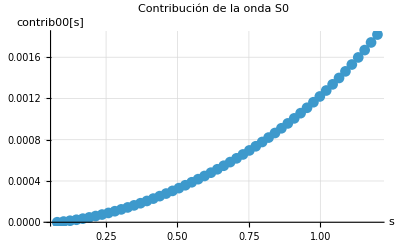

```mathematica
(*Genera una lista de puntos de s*)
sValues=Subdivide[sth+10^-3,1.2,50]; (*50 puntos,ajusta si quieres más*)

(*Evalúa contrib00[s] en cada punto,suprimiendo warnings*)
contribValues=Quiet[contrib00[#],NIntegrate::inumr]&/@sValues;

(*Grafica*)
ListLinePlot[Transpose[{sValues,contribValues}],PlotMarkers->Automatic,PlotRange->All,AxesLabel->{"s","contrib00[s]"},PlotLabel->"Contribución de la onda S0",GridLines->Automatic]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\germa\Desktop\TFG\Mathematica

```mathematica
(*Definimos el rango de s y la cantidad de puntos*)smin=sth+0.001;   (*tu límite inferior*)
smax=1.2;           (*límite superior,ajusta si quieres*)
npoints=50;         (*número de puntos,puedes aumentar para mayor precisión*)

(*Generamos la tabla de valores*)
data=Table[{s,contrib00[s]},{s,smin,smax,(smax-smin)/(npoints-1)}];

(*Exportamos a un archivo CSV*)
Export["contrib00_highenergy.csv",data]
```

contrib00_highenergy.csv

P1

```mathematica
integralSPrime1[s_?NumericQ,t_?NumericQ]:=NIntegrate[integrandI1[s, t, sp],{sp,s2, Infinity},Method->"GlobalAdaptive",MaxRecursion->20,AccuracyGoal->6];
```

```mathematica
contrib11[s_?NumericQ]:=(1/(64 Pi)) NIntegrate[x*integralSPrime1[s,tt[s,x]],{x,-1,1},Method->"GlobalAdaptive",MaxRecursion->15,AccuracyGoal->5];
```

```mathematica
data={#,contrib11[#]}&/@sValues
```

{{0.0789193,8.10922×10^-8},{0.101341,2.44456×10^-6},{0.123763,5.85507×10^-6},{0.146184,0.0000103163},{0.168606,0.0000158311},{0.191027,0.0000224016},{0.213449,0.0000300291},{0.235871,0.0000387151},{0.258292,0.0000484603},{0.280714,0.0000592655},{0.303135,0.0000711316},{0.325557,0.0000840596},{0.347979,0.0000980506},{0.3704,0.000113106},{0.392822,0.000129228},{0.415244,0.000146418},{0.437665,0.000164679},{0.460087,0.000184016},{0.482508,0.000204431},{0.50493,0.00022593},{0.527352,0.000248519},{0.549773,0.000272203},{0.572195,0.000296991},{0.594616,0.00032289},{0.617038,0.000349909},{0.63946,0.00037806},{0.661881,0.000407353},{0.684303,0.000437802},{0.706725,0.000469419},{0.729146,0.000502221},{0.751568,0.000536223},{0.773989,0.000571443},{0.796411,0.000607902},{0.818833,0.00064562},{0.841254,0.000684619},{0.863676,0.000724925},{0.886097,0.000766563},{0.908519,0.000809563},{0.930941,0.000853953},{0.953362,0.000899768},{0.975784,0.000947042},{0.998205,0.000995813},{1.02063,0.00104612},{1.04305,0.00109801},{1.06547,0.00115152},{1.08789,0.00120672},{1.11031,0.00126364},{1.13274,0.00132235},{1.15516,0.00138291},{1.17758,0.00144538},{1.2,0.00150984}}

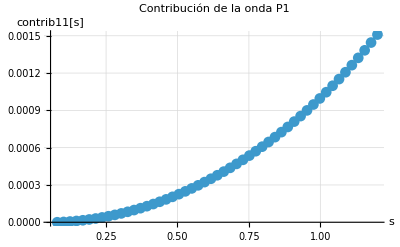

```mathematica
ListLinePlot[data,PlotMarkers->Automatic,PlotRange->All,AxesLabel->{"s","contrib11[s]"},PlotLabel->"Contribución de la onda P1",GridLines->Automatic]
```

```mathematica
(*Definimos el rango de s y la cantidad de puntos*)smin=sth+0.001;   (*tu límite inferior*)
smax=1.2;           (*límite superior,ajusta si quieres*)
npoints=50;         (*número de puntos,puedes aumentar para mayor precisión*)

(*Generamos la tabla de valores*)
data=Table[{s,contrib11[s]},{s,smin,smax,(smax-smin)/(npoints-1)}];

(*Exportamos a un archivo CSV*)
Export["contrib11_highenergy.csv",data]
```

contrib11_highenergy.csv

S2

```mathematica
integralSPrime2[s_?NumericQ,t_?NumericQ]:=NIntegrate[integrandI2[s, t, sp],{sp,s2, Infinity},Method->"GlobalAdaptive",MaxRecursion->20,AccuracyGoal->6];
```

```mathematica
contrib20[s_?NumericQ]:=(1/(64 Pi)) NIntegrate[integralSPrime2[s,tt[s,x]],{x,-1,1},Method->"GlobalAdaptive",MaxRecursion->15,AccuracyGoal->5];
```

```mathematica
contribValues=Quiet[contrib20[#],NIntegrate::inumr]&/@sValues;
```

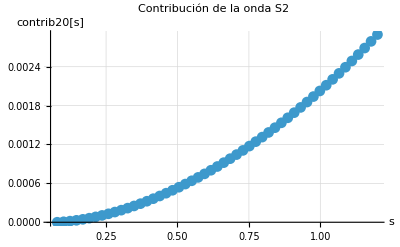

```mathematica
ListLinePlot[Transpose[{sValues,contribValues}],PlotMarkers->Automatic,PlotRange->All,AxesLabel->{"s","contrib20[s]"},PlotLabel->"Contribución de la onda S2",GridLines->Automatic]
```

```mathematica
(*Definimos el rango de s y la cantidad de puntos*)smin=sth+0.001;   (*tu límite inferior*)
smax=1.2;           (*límite superior,ajusta si quieres*)
npoints=50;         (*número de puntos,puedes aumentar para mayor precisión*)

(*Generamos la tabla de valores*)
data=Table[{s,contrib20[s]},{s,smin,smax,(smax-smin)/(npoints-1)}];

(*Exportamos a un archivo CSV*)
Export["contrib20_highenergy.csv",data]
```

contrib20_highenergy.csv

D0

```mathematica
integralSPrime0[s_?NumericQ,t_?NumericQ]:=NIntegrate[integrandI0[s, t, sp],{sp,s2, Infinity},Method->"GlobalAdaptive",MaxRecursion->20,AccuracyGoal->6];
```

```mathematica
contrib02[s_?NumericQ]:=(1/(64 Pi)) NIntegrate[LegendreP[2, x]*integralSPrime0[s,tt[s,x]],{x,-1,1},Method->"GlobalAdaptive",MaxRecursion->15,AccuracyGoal->5];
```

```mathematica
data={#,contrib02[#]}&/@sValues
```

{{0.0789193,3.44066×10^-10},{0.101341,1.93521×10^-7},{0.123763,7.59209×10^-7},{0.146184,1.72189×10^-6},{0.168606,3.10517×10^-6},{0.191027,4.93094×10^-6},{0.213449,7.2204×10^-6},{0.235871,9.99357×10^-6},{0.258292,0.0000132696},{0.280714,0.0000170668},{0.303135,0.0000214027},{0.325557,0.0000262938},{0.347979,0.0000317566},{0.3704,0.0000378064},{0.392822,0.0000444584},{0.415244,0.0000517271},{0.437665,0.0000596267},{0.460087,0.0000681712},{0.482508,0.0000773744},{0.50493,0.0000872496},{0.527352,0.0000978105},{0.549773,0.00010907},{0.572195,0.000121042},{0.594616,0.00013374},{0.617038,0.000147177},{0.63946,0.000161368},{0.661881,0.000176325},{0.684303,0.000192065},{0.706725,0.000208602},{0.729146,0.000225951},{0.751568,0.000244128},{0.773989,0.000263151},{0.796411,0.000283036},{0.818833,0.000303801},{0.841254,0.000325467},{0.863676,0.000348053},{0.886097,0.00037158},{0.908519,0.000396072},{0.930941,0.000421552},{0.953362,0.000448046},{0.975784,0.00047558},{0.998205,0.000504184},{1.02063,0.000533889},{1.04305,0.000564728},{1.06547,0.000596735},{1.08789,0.000629949},{1.11031,0.000664412},{1.13274,0.000700165},{1.15516,0.000737258},{1.17758,0.000775741},{1.2,0.000815669}}

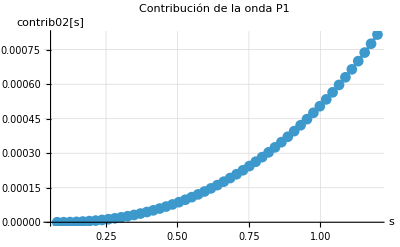

```mathematica
ListLinePlot[data,PlotMarkers->Automatic,PlotRange->All,AxesLabel->{"s","contrib02[s]"},PlotLabel->"Contribución de la onda P1",GridLines->Automatic]
```

```mathematica
data=Table[{s,contrib02[s]},{s,smin,smax,(smax-smin)/(npoints-1)}];
Export["contrib02_highenergy.csv",data]
```

contrib02_highenergy.csv

G0

```mathematica
contrib04[s_?NumericQ]:=(1/(64 Pi)) NIntegrate[LegendreP[4, x]*integralSPrime0[s,tt[s,x]],{x,-1,1},Method->"GlobalAdaptive",MaxRecursion->15,AccuracyGoal->5];
```

```mathematica
data={#,contrib04[#]}&/@sValues
```

{{0.0789193,5.65763×10^-18},{0.101341,2.02104×10^-12},{0.123763,3.40425×10^-11},{0.146184,1.87962×10^-10},{0.168606,6.43367×10^-10},{0.191027,1.691×10^-9},{0.213449,3.74605×10^-9},{0.235871,7.36101×10^-9},{0.258292,1.32377×10^-8},{0.280714,2.22749×10^-8},{0.303135,3.53616×10^-8},{0.325557,5.38348×10^-8},{0.347979,7.89798×10^-8},{0.3704,1.12358×10^-7},{0.392822,1.55606×10^-7},{0.415244,2.10636×10^-7},{0.437665,2.79514×10^-7},{0.460087,3.64458×10^-7},{0.482508,4.67854×10^-7},{0.50493,5.92287×10^-7},{0.527352,7.40293×10^-7},{0.549773,9.14999×10^-7},{0.572195,1.11937×10^-6},{0.594616,1.35667×10^-6},{0.617038,1.63029×10^-6},{0.63946,1.94379×10^-6},{0.661881,2.30091×10^-6},{0.684303,2.70553×10^-6},{0.706725,3.16178×10^-6},{0.729146,3.67389×10^-6},{0.751568,4.24632×10^-6},{0.773989,4.88369×10^-6},{0.796411,5.59082×10^-6},{0.818833,6.37276×10^-6},{0.841254,7.23475×10^-6},{0.863676,8.18227×10^-6},{0.886097,9.22104×10^-6},{0.908519,0.000010357},{0.930941,0.0000115965},{0.953362,0.000012946},{0.975784,0.0000144124},{0.998205,0.0000160029},{1.02063,0.0000177252},{1.04305,0.0000195873},{1.06547,0.0000215978},{1.08789,0.0000237656},{1.11031,0.0000261003},{1.13274,0.0000286123},{1.15516,0.0000313123},{1.17758,0.0000342122},{1.2,0.0000373246}}

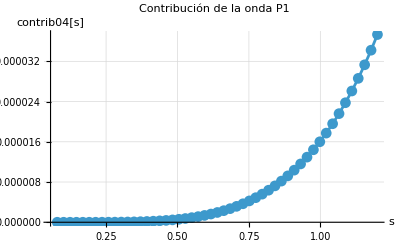

```mathematica
ListLinePlot[data,PlotMarkers->Automatic,PlotRange->All,AxesLabel->{"s","contrib04[s]"},PlotLabel->"Contribución de la onda P1",GridLines->Automatic]
```

```mathematica
data=Table[{s,contrib04[s]},{s,smin,smax,(smax-smin)/(npoints-1)}];
Export["contrib04_highenergy.csv",data]
```

contrib04_highenergy.csv

D2

```mathematica
contrib22[s_?NumericQ]:=(1/(64 Pi)) NIntegrate[LegendreP[2, x]*integralSPrime2[s,tt[s,x]],{x,-1,1},Method->"GlobalAdaptive",MaxRecursion->15,AccuracyGoal->5];
```

```mathematica
data={#,contrib22[#]}&/@sValues
```

{{0.0789193,2.93469×10^-11},{0.101341,1.99461×10^-8},{0.123763,9.04758×10^-8},{0.146184,2.30376×10^-7},{0.168606,4.56686×10^-7},{0.191027,7.84879×10^-7},{0.213449,1.229×10^-6},{0.235871,1.80177×10^-6},{0.258292,2.51475×10^-6},{0.280714,3.37841×10^-6},{0.303135,4.40224×10^-6},{0.325557,5.59485×10^-6},{0.347979,6.96406×10^-6},{0.3704,8.51696×10^-6},{0.392822,0.00001026},{0.415244,0.0000121991},{0.437665,0.0000143396},{0.460087,0.0000166865},{0.482508,0.0000192443},{0.50493,0.0000220172},{0.527352,0.0000250091},{0.549773,0.0000282237},{0.572195,0.0000316646},{0.594616,0.0000353349},{0.617038,0.000039238},{0.63946,0.000043377},{0.661881,0.000047755},{0.684303,0.0000523751},{0.706725,0.0000572404},{0.729146,0.0000623542},{0.751568,0.0000677197},{0.773989,0.0000733404},{0.796411,0.0000792199},{0.818833,0.000085362},{0.841254,0.0000917709},{0.863676,0.0000984507},{0.886097,0.000105406},{0.908519,0.000112642},{0.930941,0.000120165},{0.953362,0.000127979},{0.975784,0.000136091},{0.998205,0.000144509},{1.02063,0.000153239},{1.04305,0.00016229},{1.06547,0.00017167},{1.08789,0.000181389},{1.11031,0.000191458},{1.13274,0.000201889},{1.15516,0.000212692},{1.17758,0.000223884},{1.2,0.000235477}}

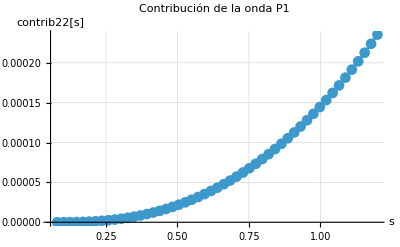

```mathematica
ListLinePlot[data,PlotMarkers->Automatic,PlotRange->All,AxesLabel->{"s","contrib22[s]"},PlotLabel->"Contribución de la onda P1",GridLines->Automatic]
```

```mathematica
data=Table[{s,contrib22[s]},{s,smin,smax,(smax-smin)/(npoints-1)}];
Export["contrib22_highenergy.csv",data]
```

contrib22_highenergy.csv

G2

```mathematica
contrib24[s_?NumericQ]:=(1/(64 Pi)) NIntegrate[LegendreP[4, x]*integralSPrime2[s,tt[s,x]],{x,-1,1},Method->"GlobalAdaptive",MaxRecursion->15,AccuracyGoal->5];
```

```mathematica
data={#,contrib24[#]}&/@sValues
```

{{0.0789193,3.31977×10^-18},{0.101341,1.22479×10^-12},{0.123763,2.09793×10^-11},{0.146184,1.16527×10^-10},{0.168606,4.00622×10^-10},{0.191027,1.05199×10^-9},{0.213449,2.32223×10^-9},{0.235871,4.53989×10^-9},{0.258292,8.11228×10^-9},{0.280714,1.35257×10^-8},{0.303135,2.1344×10^-8},{0.325557,3.2207×10^-8},{0.347979,4.68271×10^-8},{0.3704,6.5986×10^-8},{0.392822,9.05316×10^-8},{0.415244,1.21373×10^-7},{0.437665,1.5948×10^-7},{0.460087,2.05872×10^-7},{0.482508,2.61624×10^-7},{0.50493,3.27855×10^-7},{0.527352,4.05729×10^-7},{0.549773,4.9645×10^-7},{0.572195,6.01259×10^-7},{0.594616,7.21433×10^-7},{0.617038,8.58282×10^-7},{0.63946,1.01315×10^-6},{0.661881,1.18739×10^-6},{0.684303,1.38242×10^-6},{0.706725,1.59965×10^-6},{0.729146,1.84053×10^-6},{0.751568,2.10653×10^-6},{0.773989,2.39915×10^-6},{0.796411,2.71992×10^-6},{0.818833,3.07039×10^-6},{0.841254,3.45212×10^-6},{0.863676,3.86673×10^-6},{0.886097,4.31584×10^-6},{0.908519,4.80112×10^-6},{0.930941,5.32427×10^-6},{0.953362,5.88702×10^-6},{0.975784,6.49115×10^-6},{0.998205,7.13849×10^-6},{1.02063,7.83091×10^-6},{1.04305,8.57033×10^-6},{1.06547,9.35874×10^-6},{1.08789,0.0000101982},{1.11031,0.0000110909},{1.13274,0.000012039},{1.15516,0.0000130448},{1.17758,0.0000141108},{1.2,0.0000152396}}

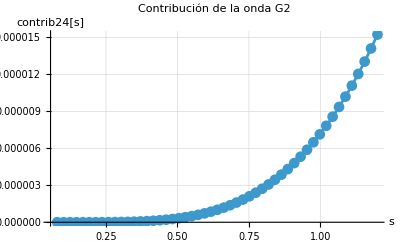

```mathematica
ListLinePlot[data,PlotMarkers->Automatic,PlotRange->All,AxesLabel->{"s","contrib24[s]"},PlotLabel->"Contribución de la onda G2",GridLines->Automatic]
```